```mathematica
NotebookInformation[]
```

{FileName→FrontEnd`FileName[{$RootDirectory,Users,ccarter,Projects_Local,dmse_git_hub,3029,development-material,Craigs_Development_Materials,Polymers},Random_Motion_Of_Polymer.nb,CharacterEncoding→UTF-8],FileModificationTime→3.85472×10^9,WindowTitle→Random_Motion_Of_Polymer.nb,MemoryModificationTime→3.85472×10^9,ModifiedInMemory→True,StorageSystem→Local,DocumentType→Notebook,MIMEType→application/vnd.wolfram.nb,StyleDefinitions→{FrontEndObject[LinkObject["i8kkj_shm", 3, 1]]4},ExpressionUUID→f221cdb3-a6df-4334-a826-7b43085048b4}

## Geometry in the frame where the blue particle moves along the x-axis:

### -Graphics-

### Equation for the position of the orange particle

```mathematica
{Δx2[s],Δy2[s]}={Δx1[s],0}  + {Cos[β[s]],Sin[β[s]]}
```

```mathematica
Cos[β[s] - Pi/2]
```

#### Let’s suppose that the rate of change of the angle β is proportional to the force projected in the radial direction of motion. ν is a “stickiness” coefficient. When ν=1, it will be rigid motion.

```mathematica
eq =D[β[s],s]== (1-ν) Sin[β[s]]
```

#### Let the initial angle be β_0

```mathematica
DSolve[  {eq,β[0]==β0},β[s],s]
```

```mathematica
β[s_,ν_,β0_]:= 2 ArcCot[ⅇ^(-s+s ν) Cot[β0/2]]
```

#### Use Rotation Transform to make the initial direction of the blue particle correspond with θ

```mathematica
DynamicModule[{p1,p2,p0},
Manipulate[
p1 = RotationTransform[θ][{s,0}];
p2 = RotationTransform[θ][{s,0} + AngleVector[β[s,ν,β0-θ]]];
Graphics[
{Blue,Circle[p1,1/2],
Orange,
Circle[p2,1/2]},
PlotRange->8{{-1,1},{-1,1}},Frame->True],
{s,0,5},
{θ,0, 2Pi},
{ν,0,1},
{β0,-Pi,Pi}
]
]
```

#### Example of 5 particles being dragged by particle #3

Note, the angles go like this: β21, β32,β33,β34,β45
The order of the angles changes.
The particles to the left of particle 3 have decreasing indices; the particles to the right have increasing indices.

```mathematica
DynamicModule[{d1,d2,d3,d4,d5, β33 =0},Manipulate[
Graphics[
d3 = s AngleVector[β[s,ν,β33]];
d4 = d3 + AngleVector[β[s,ν,β34-θ]];
d5 = d4 + AngleVector[β[s,ν,β45-θ]];
d2 = d3 + AngleVector[β[s,ν,β32-θ]];
d1 = d2 + AngleVector[β[s,ν,β21-θ]];

{Blue,
Circle[RotationMatrix[θ].d3,1/2],
Orange,
Circle[RotationMatrix[θ].d4,1/2],
Circle[RotationMatrix[θ].d5,1/2],
Circle[RotationMatrix[θ].d2,1/2],
Circle[RotationMatrix[θ].d1,1/2](*,
Line[{{0,0},1AngleVector[θ]}],
Blue,Orange,
Line[{RotationMatrix[θ].AngleVector[β[0,ν,β0-θ] ],RotationMatrix[θ].({s,0}+AngleVector[β[s,ν,β0-θ]])}]*)
,Black,
Text[1,RotationMatrix[θ].d1],
Text[2,RotationMatrix[θ].d2],
Text[3,RotationMatrix[θ].d3],
Text[4,RotationMatrix[θ].d4],
Text[5,RotationMatrix[θ].d5]


},
PlotRange->3{{-1,1},{-1,1}},Frame->True
],
{s,0,1},
{θ,0, 2Pi},
{ν,0,1},
{β45,-Pi,Pi},
{{β34,Pi/2},-Pi,Pi},
{{β32,-1},-Pi,Pi},
{{β21,-1},-Pi,Pi}
]
]
```

#### Illustration of the propagation of disturbance behavior of the subsequent points.

```mathematica
Clear[s,ν,θ];β33=0;
d3 = s AngleVector[β[s,ν,β33]];
d4 = d3 + AngleVector[β[s,ν,β34-θ]];
d5 = d4 + AngleVector[β[s,ν,β45-θ]];
d2 = d3 + AngleVector[β[s,ν,β32-θ]];
d1 = d2 + AngleVector[β[s,ν,β21-θ]];
RotationTransform[θ][{d1,d2,d3,d4,d5}]//FullSimplify//Grid
```

#### Note the recursive behavior of the terms as they propagate from the preceding link in the chain until they reach the particle that was set in motion (above, that particle was 3). Each term is the sum of its predecessor by sines and cosines of an “reduced” angle: We can precompute all of these reduced angles efficiently and then use a recursive definition to compute the displacements

```mathematica
precompute[positions_,perturbedIndex_,s_,ν_, θ_]:= Block[
{
dp = Differences[positions],
betaList,
diffs,
reducedAngles
},
betaList =ArcTan@@@ Join[-dp[[1;;perturbedIndex-1]],dp[[perturbedIndex;;-1]]] ;
reducedAngles=θ +2 ArcCot[ⅇ^(-s+s ν)Cot[(betaList-θ)/2]];
reducedAngles=Insert[reducedAngles,θ,perturbedIndex];
Transpose@{Cos[reducedAngles],Sin[reducedAngles]}]
```

For example:

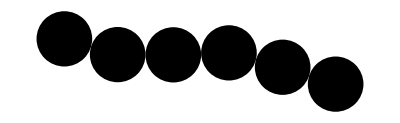

```mathematica
positions = AnglePath[RandomReal[{-.3,.3},5]];
Graphics[Disk[#,1/2]&/@positions]
```

```mathematica
Grid[precompute[positions,3,s,ν,θ],Frame->All]
```

Cos[θ+2 ArcCot[ⅇ^(-s+s ν) Cot[1/2 (2.85259-θ)]]] | Sin[θ+2 ArcCot[ⅇ^(-s+s ν) Cot[1/2 (2.85259-θ)]]]
Cos[θ+2 ArcCot[ⅇ^(-s+s ν) Cot[1/2 (3.1373-θ)]]] | Sin[θ+2 ArcCot[ⅇ^(-s+s ν) Cot[1/2 (3.1373-θ)]]]
Cos[θ] | Sin[θ]
Cos[θ+2 ArcCot[ⅇ^(-s+s ν) Cot[1/2 (0.0357436-θ)]]] | Sin[θ+2 ArcCot[ⅇ^(-s+s ν) Cot[1/2 (0.0357436-θ)]]]
Cos[θ+2 ArcCot[ⅇ^(-s+s ν) Cot[1/2 (-0.263076-θ)]]] | Sin[θ+2 ArcCot[ⅇ^(-s+s ν) Cot[1/2 (-0.263076-θ)]]]
Cos[θ+2 ArcCot[ⅇ^(-s+s ν) Cot[1/2 (-0.310738-θ)]]] | Sin[θ+2 ArcCot[ⅇ^(-s+s ν) Cot[1/2 (-0.310738-θ)]]]

#### Here is the displacement function. It creates a recursive function each time it is called, and then uses recursion to compute each displacement, and memoizes (i.e., remembers) each computation.

```mathematica
displacements[perturbedIndex_,positionList_,s_,ν_,θ_]:= 
Block[{newPositions,betaList,Δ  },
Δ=precompute[positionList,perturbedIndex,s,ν,θ];
newPositions[perturbedIndex] =positionList[[perturbedIndex]]+s AngleVector[θ];
newPositions[index_] := newPositions[index]=
Which[
index> perturbedIndex,newPositions[index-1] + Δ[[index]],
True,newPositions[index+1] + Δ[[index]]];
newPositions/@Range[Length[Δ]]
]
```

Note: This function doesn’t check for collisions. We will fix that up later.

#### For example:

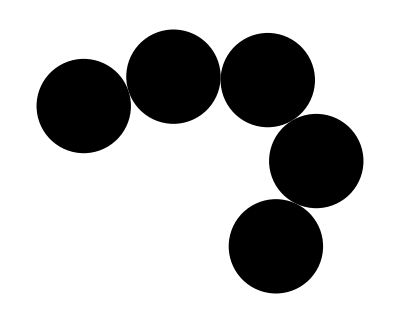

```mathematica
positions = AnglePath[RandomReal[{-1,1},4]];
Graphics[Disk[#,1/2]&/@positions]
```

```mathematica
displacements[2,positions,s,ν,θ]//Short
displacements[2,positions,.1,.1,Pi/3]
```

{{0.950369+s Cos[θ]+Cos[θ+2 ArcCot[ⅇ^(-s+s ν) Cot[1/2 (-«18»-θ)]]],«1»},«4»}

{{0.0696593,0.0319687},{1.00037,0.397726},{1.9935,0.280687},{2.43965,-0.614269},{2.00563,-1.51517}}

#### Visualization:

```mathematica
chainGraphic[positions_]:= 
{FaceForm[Orange],EdgeForm[Black],Disk[#,1/2]&/@(positions),
MapIndexed[Text[#2[[1]],#1]&,(positions)]}
```

```mathematica
DynamicModule[
{positions = AnglePath[RandomReal[{-1,1},8]]},
Manipulate[
If[reset,positions = AnglePath[RandomReal[{-1,1},8]];reset=False];
Graphics[
{ chainGraphic[displacements[i,positions,s,0,θ]],
{Red,PointSize[0.01],Point[positions[[i]]],Arrow[{positions[[i]],positions[[i]]+6 AngleVector[θ]}]}},
PlotRange->p{{-1,1},{-1,1}},Frame->True
],
{{s,0,Style["Displacement",14]},0,3},
{{θ,Pi/2,Style["Displacement Direction",14]},-Pi, Pi},
{{i,1,Style["Particle to Displace",14]},Range[Length[positions]]},
{{p,10,Style["Zoom",14]},2,20},
Delimiter,
{{reset,False,Style["Reset Initial Configuration",14]},{True,False}}
]
]
```

#### Using the visualization tool, you will see that the chain will occasionally “intersect” itself. This is because we have not included a collision detection algorithm yet. We will do that below. But, first let’s use our current model to illustrate how we will implement Brownian motion of a polymer.

### Random Motion

#### We will model the motion of an isolated particle by assuming that a temperature bath applies a random force to a randomly chosen atom in the chain.

```mathematica
positions = AnglePath[RandomReal[{-0.5,0.5},12]];
currentGraphic = Graphics[chainGraphic[positions],PlotRange->15{{-1,1},{-1,1}},Frame->True];
Dynamic[currentGraphic]
```

```mathematica
With[{stiffness = 0, relativeTemperature = 0.2},
Do[
With[{whichParticle =RandomInteger[{1,Length[positions]}],
perturbation = RandomVariate[MaxwellDistribution[relativeTemperature]],
angle = RandomReal[2Pi]
},
(*positions =(Mean[positions]+#)&/@displacements[whichParticle,positions,perturbation,stiffness,angle];*)positions=displacements[whichParticle,positions,perturbation,stiffness,angle];
currentGraphic = Graphics[chainGraphic[positions],PlotRange->15{{-1,1},{-1,1}},Frame->True];
];Pause[0.05],
{100}
]
]
```

### Collision Detection and Avoidance (seems to be working, but needs comments and good examle)

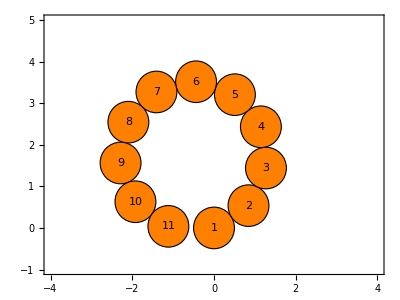

```mathematica
positions = AnglePath[ConstantArray[0.565,10]];
Graphics[chainGraphic[positions],PlotRange->{{-4,4},{-1,5}},Frame->True]
```

```mathematica
Manipulate[
Graphics[chainGraphic[displacements[11,positions,s,.1,0]],
PlotRange->{{-4,4},{-1,5}},Frame->True],
{s,0,1}
]
```

```mathematica
Union@Flatten[DistanceMatrix[displacements[11,positions,.126,.1,0]]+ IdentityMatrix[Length[positions]]]//N
```

{0.488437,1.,1.,1.,1.43435,1.44781,1.90105,1.90432,1.90517,1.91311,1.91434,1.92321,1.92434,1.93128,1.93203,2.2055,2.28766,2.30931,2.62024,2.62186,2.64333,2.64731,2.67954,2.68407,2.71442,2.71803,2.82552,2.83523,2.96807,2.9935,3.08771,3.11219,3.11858,3.1789,3.1802,3.19001,3.23468,3.24939,3.26255,3.27203,3.28591,3.29148,3.367,3.38128,3.3945,3.41818,3.5005,3.51777}

One approach would be to limit the magnitude of the perturbation distance so that no  collisions occur. For example:

```mathematica
Manipulate[
Union@Flatten[DistanceMatrix[displacements[11,positions,s,.1,0]]+ IdentityMatrix[Length[positions]]][[1;;10]],
{s,0,6}
]
```

This would be fairly easy to code.

Another approach would be to detect collisions in the recursive part in the displacements function.  If a collision is found, then that displacement is limited.

```mathematica
(*displacementsNew[perturbedIndex_,positionList_,s_,ν_,θ_]:= 
Block[{displacement,betaList,Δ , computedPositions,collisionDistance },
Δ=precompute[positionList,perturbedIndex,s,ν,θ];
displacement[perturbedIndex] =positionList[[perturbedIndex]]+s AngleVector[θ];
computedPositions = {displacement[perturbedIndex]};
Identity[{perturbedIndex,computedPositions}];
displacement[index_] := displacement[index]=
Which[
index> perturbedIndex,
With[{testPoint=displacement[index-1] + Δ[[index]]},
Echo[collisionDistance = Nearest[computedPositions->"Distance"][testPoint][[1]]];
Which[collisionDistance>= 1,Identity[ {index,index> perturbedIndex,AppendTo[computedPositions,testPoint]}];testPoint,
True, AppendTo[computedPositions,displacement[index-1]];displacement[index-1]]
],
True,
With[{testPoint=displacement[index+1] + Δ[[index]]},
Echo[collisionDistance = Nearest[computedPositions->"Distance"][testPoint][[1]]];
Which[collisionDistance>= 1,Identity[{index,index> perturbedIndex, AppendTo[computedPositions,testPoint]}];testPoint,
True, AppendTo[computedPositions,displacement[index+1]];displacement[index+1]]
]
];
displacement/@Range[Length[Δ]]
]*)
```

```mathematica
Clear[displacementsNew]
```

```mathematica
Options[displacementsNew]={"Return"->"Result"}
```

{Return→Result}

Need to fix filter for next nearest neighbors below.

```mathematica
displacementsNew[perturbedIndex_,positionList_,s_,ν_,θ_,OptionsPattern[]]:= 
Block[{displacement,betaList,Δ , computedPositions,collisionDistance,results,overlap,minDistances },
(*Echo[s];*)
Δ=precompute[positionList,perturbedIndex,s,ν,θ];
displacement[perturbedIndex] =positionList[[perturbedIndex]]+s AngleVector[θ];
computedPositions = {displacement[perturbedIndex]};
(*#1*)
 displacement[index_] := displacement[index]=
Module[
{testPoint=displacement[index-Sign[index-perturbedIndex] ]+ Δ[[index]],
checkNearby ,collisions,notNearestNeighbors},
checkNearby =Nearest[computedPositions->All][testPoint,All];
(*#2*)
notNearestNeighbors=Select[Abs[#Index - perturbedIndex]> 1&][checkNearby];
(*Echo[notNearestNeighbors];*)
Which[
notNearestNeighbors =={},Sow[Nothing],
True,
collisions =Select[#Distance < 1&][notNearestNeighbors];
(*#3*)
If[collisions !={},Throw[collisions[[1,"Distance"]]]];
Echo[notNearestNeighbors,"nnn"];
Sow[MinimalBy[#Distance&][notNearestNeighbors][[1,"Distance"]]]
];
(*#4*)
AppendTo[computedPositions,testPoint];
testPoint
];
(*#5*)
overlap = Catch[{results,minDistances}= Reap[displacement/@Range[Length[Δ]]]];
Which[
ListQ[overlap] && OptionValue["Return"]!="Distance",
results,
(*#6*)
ListQ[overlap] && OptionValue["Return"]=="Distance",
Echo[minDistances];
Echo[Min[minDistances],"min dists"],

NumericQ[overlap] && OptionValue["Return"]=="Distance",
Return[overlap],
(*#7*)
NumericQ[overlap] && overlap<1,
findNonTouchingDisplacement[perturbedIndex,positionList,{s,0},ν,θ]
]
]
```

Code Footnotes:
#1) This is a recursive function....
#2)  Because nearest neighbors are always distance=1, we don’t want to include....
#3)
#4)
#5)
#6)
#7)

```mathematica
findNonTouchingDisplacement[perturbedIndex_,positionList_,{sProducingDistanceLessThan1_,sProducingDistanceGreaterThan1_},ν_,θ_]:=
Module[
{greaterThan1 = sProducingDistanceGreaterThan1, lessThan1 = sProducingDistanceLessThan1,
search,
currentDistance,
tries = 1, maxtries = 50,lastGreater=0},
search = Mean[Echo@{lessThan1,greaterThan1}];
currentDistance = 0;
Echo[currentDistance];
(*#1*)
While[Abs[greaterThan1-lessThan1]> 0.0001 (*&& currentDistance<1*)&& ++tries < maxtries,
(*#2*)
currentDistance = displacementsNew[perturbedIndex,positionList,search,ν,θ,"Return"->"Distance"];
search = Mean[{lessThan1,greaterThan1}];
Which[
(*#3*)
currentDistance<1,lessThan1= search,
True,lastGreater=greaterThan1= search
];
Echo[{search,{lessThan1,greaterThan1},currentDistance<1,NumberForm[currentDistance,100]}];
];
If[tries>= maxtries,Print["Binary Search went weirdly wrong"]];
Echo[lastGreater,"last greater"];
(*#4*)
displacementsNew[perturbedIndex,positionList,lastGreater,ν,θ]
]
```

Code Footnotes:
#1)
#2)
#3)
#4)

```mathematica
test=displacementsNew[11,positions,.5,.1,0]
```

nnn  {<|Element→{-0.616202,0.038069},Index→1,Distance→1.|>}

nnn  {<|Element→{-1.53258,0.43839},Index→2,Distance→1.|>,<|Element→{-0.616202,0.038069},Index→1,Distance→1.95825|>}

nnn  {<|Element→{-2.21388,1.17039},Index→3,Distance→1.|>,<|Element→{-1.53258,0.43839},Index→2,Distance→1.93884|>,<|Element→{-0.616202,0.038069},Index→1,Distance→2.79799|>}

nnn  {<|Element→{-2.46482,2.13839},Index→4,Distance→1.|>,<|Element→{-2.21388,1.17039},Index→3,Distance→1.89964|>,<|Element→{-1.53258,0.43839},Index→2,Distance→2.68648|>,<|Element→{-0.616202,0.038069},Index→1,Distance→3.36828|>}

nnn  {<|Element→{-2.09148,3.06609},Index→5,Distance→1.|>,<|Element→{-2.46482,2.13839},Index→4,Distance→1.84154|>,<|Element→{-2.21388,1.17039},Index→3,Distance→2.50305|>,<|Element→{-1.53258,0.43839},Index→2,Distance→3.02719|>,<|Element→{-0.616202,0.038069},Index→1,Distance→3.44915|>}

nnn  {<|Element→{-1.16532,3.44322},Index→6,Distance→1.|>,<|Element→{-2.09148,3.06609},Index→5,Distance→1.81064|>,<|Element→{-2.46482,2.13839},Index→4,Distance→2.3354|>,<|Element→{-2.21388,1.17039},Index→3,Distance→2.64068|>,<|Element→{-1.53258,0.43839},Index→2,Distance→2.82492|>,<|Element→{-0.616202,0.038069},Index→1,Distance→2.95281|>}

nnn  {<|Element→{-0.283278,2.97205},Index→7,Distance→1.|>,<|Element→{-1.16532,3.44322},Index→6,Distance→1.84855|>,<|Element→{-0.616202,0.038069},Index→1,Distance→2.07425|>,<|Element→{-1.53258,0.43839},Index→2,Distance→2.20575|>,<|Element→{-2.09148,3.06609},Index→5,Distance→2.34863|>,<|Element→{-2.21388,1.17039},Index→3,Distance→2.37842|>,<|Element→{-2.46482,2.13839},Index→4,Distance→2.47708|>}

nnn  {<|Element→{0.00922211,2.01578},Index→8,Distance→1.|>,<|Element→{-0.616202,0.038069},Index→1,Distance→1.07443|>,<|Element→{-1.53258,0.43839},Index→2,Distance→1.37874|>,<|Element→{-0.283278,2.97205},Index→7,Distance→1.90567|>,<|Element→{-2.21388,1.17039},Index→3,Distance→1.91148|>,<|Element→{-2.46482,2.13839},Index→4,Distance→2.41097|>,<|Element→{-1.16532,3.44322},Index→6,Distance→2.52755|>,<|Element→{-2.09148,3.06609},Index→5,Distance→2.68123|>}

{0.5,0}

0

nnn  {<|Element→{-0.866202,0.038069},Index→1,Distance→1.|>}

nnn  {<|Element→{-1.7381,0.527763},Index→2,Distance→1.|>,<|Element→{-0.866202,0.038069},Index→1,Distance→1.94109|>}

nnn  {<|Element→{-2.27979,1.36834},Index→3,Distance→1.|>,<|Element→{-1.7381,0.527763},Index→2,Distance→1.92726|>,<|Element→{-0.866202,0.038069},Index→1,Distance→2.74151|>}

nnn  {<|Element→{-2.31119,2.36785},Index→4,Distance→1.|>,<|Element→{-2.27979,1.36834},Index→3,Distance→1.90683|>,<|Element→{-1.7381,0.527763},Index→2,Distance→2.67585|>,<|Element→{-0.866202,0.038069},Index→1,Distance→3.28974|>}

nnn  {<|Element→{-1.76194,3.20351},Index→5,Distance→1.|>,<|Element→{-2.31119,2.36785},Index→4,Distance→1.88579|>,<|Element→{-2.27979,1.36834},Index→3,Distance→2.59665|>,<|Element→{-1.7381,0.527763},Index→2,Distance→3.12221|>,<|Element→{-0.866202,0.038069},Index→1,Distance→3.47113|>}

nnn  {<|Element→{-0.809665,3.50874},Index→6,Distance→1.|>,<|Element→{-1.76194,3.20351},Index→5,Distance→1.87709|>,<|Element→{-2.31119,2.36785},Index→4,Distance→2.53992|>,<|Element→{-2.27979,1.36834},Index→3,Distance→2.96834|>,<|Element→{-1.7381,0.527763},Index→2,Distance→3.18908|>,<|Element→{-0.866202,0.038069},Index→1,Distance→3.23798|>}

nnn  {<|Element→{0.113478,3.12429},Index→7,Distance→1.|>,<|Element→{-0.809665,3.50874},Index→6,Distance→1.88796|>,<|Element→{-1.76194,3.20351},Index→5,Distance→2.54405|>,<|Element→{-0.866202,0.038069},Index→1,Distance→2.65023|>,<|Element→{-1.7381,0.527763},Index→2,Distance→2.89979|>,<|Element→{-2.31119,2.36785},Index→4,Distance→2.90967|>,<|Element→{-2.27979,1.36834},Index→3,Distance→3.00746|>}

nnn  {<|Element→{0.596024,2.24842},Index→8,Distance→1.|>,<|Element→{-0.866202,0.038069},Index→1,Distance→1.82549|>,<|Element→{0.113478,3.12429},Index→7,Distance→1.90953|>,<|Element→{-1.7381,0.527763},Index→2,Distance→2.34889|>,<|Element→{-0.809665,3.50874},Index→6,Distance→2.60592|>,<|Element→{-2.27979,1.36834},Index→3,Distance→2.77805|>,<|Element→{-1.76194,3.20351},Index→5,Distance→2.98338|>,<|Element→{-2.31119,2.36785},Index→4,Distance→3.02019|>}

{0.25,{0.25,0},True,0.872141333467643}

nnn  {<|Element→{-0.866202,0.038069},Index→1,Distance→1.|>}

nnn  {<|Element→{-1.7381,0.527763},Index→2,Distance→1.|>,<|Element→{-0.866202,0.038069},Index→1,Distance→1.94109|>}

nnn  {<|Element→{-2.27979,1.36834},Index→3,Distance→1.|>,<|Element→{-1.7381,0.527763},Index→2,Distance→1.92726|>,<|Element→{-0.866202,0.038069},Index→1,Distance→2.74151|>}

nnn  {<|Element→{-2.31119,2.36785},Index→4,Distance→1.|>,<|Element→{-2.27979,1.36834},Index→3,Distance→1.90683|>,<|Element→{-1.7381,0.527763},Index→2,Distance→2.67585|>,<|Element→{-0.866202,0.038069},Index→1,Distance→3.28974|>}

nnn  {<|Element→{-1.76194,3.20351},Index→5,Distance→1.|>,<|Element→{-2.31119,2.36785},Index→4,Distance→1.88579|>,<|Element→{-2.27979,1.36834},Index→3,Distance→2.59665|>,<|Element→{-1.7381,0.527763},Index→2,Distance→3.12221|>,<|Element→{-0.866202,0.038069},Index→1,Distance→3.47113|>}

nnn  {<|Element→{-0.809665,3.50874},Index→6,Distance→1.|>,<|Element→{-1.76194,3.20351},Index→5,Distance→1.87709|>,<|Element→{-2.31119,2.36785},Index→4,Distance→2.53992|>,<|Element→{-2.27979,1.36834},Index→3,Distance→2.96834|>,<|Element→{-1.7381,0.527763},Index→2,Distance→3.18908|>,<|Element→{-0.866202,0.038069},Index→1,Distance→3.23798|>}

nnn  {<|Element→{0.113478,3.12429},Index→7,Distance→1.|>,<|Element→{-0.809665,3.50874},Index→6,Distance→1.88796|>,<|Element→{-1.76194,3.20351},Index→5,Distance→2.54405|>,<|Element→{-0.866202,0.038069},Index→1,Distance→2.65023|>,<|Element→{-1.7381,0.527763},Index→2,Distance→2.89979|>,<|Element→{-2.31119,2.36785},Index→4,Distance→2.90967|>,<|Element→{-2.27979,1.36834},Index→3,Distance→3.00746|>}

nnn  {<|Element→{0.596024,2.24842},Index→8,Distance→1.|>,<|Element→{-0.866202,0.038069},Index→1,Distance→1.82549|>,<|Element→{0.113478,3.12429},Index→7,Distance→1.90953|>,<|Element→{-1.7381,0.527763},Index→2,Distance→2.34889|>,<|Element→{-0.809665,3.50874},Index→6,Distance→2.60592|>,<|Element→{-2.27979,1.36834},Index→3,Distance→2.77805|>,<|Element→{-1.76194,3.20351},Index→5,Distance→2.98338|>,<|Element→{-2.31119,2.36785},Index→4,Distance→3.02019|>}

{0.125,{0.125,0},True,0.872141333467643}

nnn  {<|Element→{-0.991202,0.038069},Index→1,Distance→1.|>}

nnn  {<|Element→{-1.83332,0.577356},Index→2,Distance→1.|>,<|Element→{-0.991202,0.038069},Index→1,Distance→1.9312|>}

nnn  {<|Element→{-2.29074,1.46661},Index→3,Distance→1.|>,<|Element→{-1.83332,0.577356},Index→2,Distance→1.92319|>,<|Element→{-0.991202,0.038069},Index→1,Distance→2.71421|>}

nnn  {<|Element→{-2.20983,2.46333},Index→4,Distance→1.|>,<|Element→{-2.29074,1.46661},Index→3,Distance→1.91317|>,<|Element→{-1.83332,0.577356},Index→2,Distance→2.67959|>,<|Element→{-0.991202,0.038069},Index→1,Distance→3.26237|>}

nnn  {<|Element→{-1.58689,3.24559},Index→5,Distance→1.|>,<|Element→{-2.20983,2.46333},Index→4,Distance→1.90446|>,<|Element→{-2.29074,1.46661},Index→3,Distance→2.6437|>,<|Element→{-1.83332,0.577356},Index→2,Distance→3.18069|>,<|Element→{-0.991202,0.038069},Index→1,Distance→3.50079|>}

nnn  {<|Element→{-0.625182,3.51967},Index→6,Distance→1.|>,<|Element→{-1.58689,3.24559},Index→5,Distance→1.90123|>,<|Element→{-2.20983,2.46333},Index→4,Distance→2.62084|>,<|Element→{-2.29074,1.46661},Index→3,Distance→3.11329|>,<|Element→{-1.83332,0.577356},Index→2,Distance→3.36841|>,<|Element→{-0.991202,0.038069},Index→1,Distance→3.39579|>}

nnn  {<|Element→{0.312968,3.17344},Index→7,Distance→1.|>,<|Element→{-0.625182,3.51967},Index→6,Distance→1.9053|>,<|Element→{-1.58689,3.24559},Index→5,Distance→2.62244|>,<|Element→{-0.991202,0.038069},Index→1,Distance→2.97066|>,<|Element→{-2.20983,2.46333},Index→4,Distance→3.08905|>,<|Element→{-1.83332,0.577356},Index→2,Distance→3.23733|>,<|Element→{-2.29074,1.46661},Index→3,Distance→3.28805|>}

nnn  {<|Element→{0.877048,2.34772},Index→8,Distance→1.|>,<|Element→{0.312968,3.17344},Index→7,Distance→1.91439|>,<|Element→{-0.991202,0.038069},Index→1,Distance→2.29146|>,<|Element→{-0.625182,3.51967},Index→6,Distance→2.64764|>,<|Element→{-1.83332,0.577356},Index→2,Distance→2.82931|>,<|Element→{-1.58689,3.24559},Index→5,Distance→3.11962|>,<|Element→{-2.29074,1.46661},Index→3,Distance→3.18204|>,<|Element→{-2.20983,2.46333},Index→4,Distance→3.29358|>}

nnn  {<|Element→{0.889072,1.34779},Index→9,Distance→1.|>,<|Element→{-0.991202,0.038069},Index→1,Distance→1.43899|>,<|Element→{0.877048,2.34772},Index→8,Distance→1.92431|>,<|Element→{-1.83332,0.577356},Index→2,Distance→2.21001|>,<|Element→{0.312968,3.17344},Index→7,Distance→2.68409|>,<|Element→{-2.29074,1.46661},Index→3,Distance→2.83894|>,<|Element→{-0.625182,3.51967},Index→6,Distance→3.19042|>,<|Element→{-2.20983,2.46333},Index→4,Distance→3.25191|>,<|Element→{-1.58689,3.24559},Index→5,Distance→3.38257|>}

{0.0625,{0.0625,0},True,0.4934085277742543}

nnn  {<|Element→{-1.0537,0.038069},Index→1,Distance→1.|>}

nnn  {<|Element→{-1.87867,0.603248},Index→2,Distance→1.|>,<|Element→{-1.0537,0.038069},Index→1,Distance→1.92601|>}

nnn  {<|Element→{-2.29048,1.51452},Index→3,Distance→1.|>,<|Element→{-1.87867,0.603248},Index→2,Distance→1.92174|>,<|Element→{-1.0537,0.038069},Index→1,Distance→2.70133|>}

nnn  {<|Element→{-2.154,2.50516},Index→4,Distance→1.|>,<|Element→{-2.29048,1.51452},Index→3,Distance→1.91682|>,<|Element→{-1.87867,0.603248},Index→2,Distance→2.68368|>,<|Element→{-1.0537,0.038069},Index→1,Distance→3.25218|>}

nnn  {<|Element→{-1.49784,3.25977},Index→5,Distance→1.|>,<|Element→{-2.154,2.50516},Index→4,Distance→1.91289|>,<|Element→{-2.29048,1.51452},Index→3,Distance→2.66671|>,<|Element→{-1.87867,0.603248},Index→2,Distance→3.21202|>,<|Element→{-1.0537,0.038069},Index→1,Distance→3.52017|>}

nnn  {<|Element→{-0.532125,3.51939},Index→6,Distance→1.|>,<|Element→{-1.49784,3.25977},Index→5,Distance→1.9115|>,<|Element→{-2.154,2.50516},Index→4,Distance→2.65649|>,<|Element→{-2.29048,1.51452},Index→3,Distance→3.18062|>,<|Element→{-1.87867,0.603248},Index→2,Distance→3.45625|>,<|Element→{-1.0537,0.038069},Index→1,Distance→3.47715|>}

nnn  {<|Element→{0.412423,3.19101},Index→7,Distance→1.|>,<|Element→{-0.532125,3.51939},Index→6,Distance→1.91326|>,<|Element→{-1.49784,3.25977},Index→5,Distance→2.65719|>,<|Element→{-1.0537,0.038069},Index→1,Distance→3.13282|>,<|Element→{-2.154,2.50516},Index→4,Distance→3.16967|>,<|Element→{-1.87867,0.603248},Index→2,Distance→3.40071|>,<|Element→{-2.29048,1.51452},Index→3,Distance→3.41864|>}

nnn  {<|Element→{1.01364,2.39193},Index→8,Distance→1.|>,<|Element→{0.412423,3.19101},Index→7,Distance→1.9174|>,<|Element→{-1.0537,0.038069},Index→1,Distance→2.52975|>,<|Element→{-0.532125,3.51939},Index→6,Distance→2.66851|>,<|Element→{-1.87867,0.603248},Index→2,Distance→3.06433|>,<|Element→{-1.49784,3.25977},Index→5,Distance→3.18351|>,<|Element→{-2.29048,1.51452},Index→3,Distance→3.37444|>,<|Element→{-2.154,2.50516},Index→4,Distance→3.4212|>}

nnn  {<|Element→{1.08181,1.39425},Index→9,Distance→1.|>,<|Element→{-1.0537,0.038069},Index→1,Distance→1.73025|>,<|Element→{1.01364,2.39193},Index→8,Distance→1.92231|>,<|Element→{-1.87867,0.603248},Index→2,Distance→2.49059|>,<|Element→{0.412423,3.19101},Index→7,Distance→2.6859|>,<|Element→{-2.29048,1.51452},Index→3,Distance→3.06896|>,<|Element→{-0.532125,3.51939},Index→6,Distance→3.21667|>,<|Element→{-2.154,2.50516},Index→4,Distance→3.40767|>,<|Element→{-1.49784,3.25977},Index→5,Distance→3.46296|>}

{0.03125,{0.03125,0},True,0.804801595007059}

nnn  {<|Element→{-1.08495,0.038069},Index→1,Distance→1.|>}

nnn  {<|Element→{-1.90072,0.616441},Index→2,Distance→1.|>,<|Element→{-1.08495,0.038069},Index→1,Distance→1.92338|>}

nnn  {<|Element→{-2.28892,1.53802},Index→3,Distance→1.|>,<|Element→{-1.90072,0.616441},Index→2,Distance→1.92117|>,<|Element→{-1.08495,0.038069},Index→1,Distance→2.69515|>}

nnn  {<|Element→{-2.12495,2.52448},Index→4,Distance→1.|>,<|Element→{-2.28892,1.53802},Index→3,Distance→1.91875|>,<|Element→{-1.90072,0.616441},Index→2,Distance→2.68626|>,<|Element→{-1.08495,0.038069},Index→1,Distance→3.248|>}

nnn  {<|Element→{-1.45306,3.26514},Index→5,Distance→1.|>,<|Element→{-2.12495,2.52448},Index→4,Distance→1.91688|>,<|Element→{-2.28892,1.53802},Index→3,Distance→2.67802|>,<|Element→{-1.90072,0.616441},Index→2,Distance→3.2281|>,<|Element→{-1.08495,0.038069},Index→1,Distance→3.53097|>}

nnn  {<|Element→{-0.485503,3.51779},Index→6,Distance→1.|>,<|Element→{-1.45306,3.26514},Index→5,Distance→1.91623|>,<|Element→{-2.12495,2.52448},Index→4,Distance→2.67319|>,<|Element→{-2.28892,1.53802},Index→3,Distance→3.21297|>,<|Element→{-1.90072,0.616441},Index→2,Distance→3.49958|>,<|Element→{-1.08495,0.038069},Index→1,Distance→3.5183|>}

nnn  {<|Element→{0.461999,3.19804},Index→7,Distance→1.|>,<|Element→{-0.485503,3.51779},Index→6,Distance→1.91705|>,<|Element→{-1.45306,3.26514},Index→5,Distance→2.67352|>,<|Element→{-2.12495,2.52448},Index→4,Distance→3.20777|>,<|Element→{-1.08495,0.038069},Index→1,Distance→3.21386|>,<|Element→{-1.90072,0.616441},Index→2,Distance→3.48079|>,<|Element→{-2.28892,1.53802},Index→3,Distance→3.48142|>}

nnn  {<|Element→{1.08087,2.41254},Index→8,Distance→1.|>,<|Element→{0.461999,3.19804},Index→7,Distance→1.91903|>,<|Element→{-1.08495,0.038069},Index→1,Distance→2.64919|>,<|Element→{-0.485503,3.51779},Index→6,Distance→2.67888|>,<|Element→{-1.90072,0.616441},Index→2,Distance→3.18015|>,<|Element→{-1.45306,3.26514},Index→5,Distance→3.21435|>,<|Element→{-2.28892,1.53802},Index→3,Distance→3.46799|>,<|Element→{-2.12495,2.52448},Index→4,Distance→3.48265|>}

nnn  {<|Element→{1.17697,1.41717},Index→9,Distance→1.|>,<|Element→{-1.08495,0.038069},Index→1,Distance→1.8765|>,<|Element→{1.08087,2.41254},Index→8,Distance→1.92147|>,<|Element→{-1.90072,0.616441},Index→2,Distance→2.62994|>,<|Element→{0.461999,3.19804},Index→7,Distance→2.68736|>,<|Element→{-2.28892,1.53802},Index→3,Distance→3.18243|>,<|Element→{-0.485503,3.51779},Index→6,Distance→3.23038|>,<|Element→{-2.12495,2.52448},Index→4,Distance→3.48419|>,<|Element→{-1.45306,3.26514},Index→5,Distance→3.50285|>}

{0.015625,{0.015625,0},True,0.960788210557326}

nnn  {<|Element→{-1.10058,0.038069},Index→1,Distance→1.|>}

nnn  {<|Element→{-1.91159,0.623094},Index→2,Distance→1.|>,<|Element→{-1.10058,0.038069},Index→1,Distance→1.92205|>}

nnn  {<|Element→{-2.28778,1.54964},Index→3,Distance→1.|>,<|Element→{-1.91159,0.623094},Index→2,Distance→1.92093|>,<|Element→{-1.10058,0.038069},Index→1,Distance→2.69214|>}

nnn  {<|Element→{-2.11016,2.53374},Index→4,Distance→1.|>,<|Element→{-2.28778,1.54964},Index→3,Distance→1.91973|>,<|Element→{-1.91159,0.623094},Index→2,Distance→2.68768|>,<|Element→{-1.10058,0.038069},Index→1,Distance→3.24614|>}

nnn  {<|Element→{-1.43063,3.26739},Index→5,Distance→1.|>,<|Element→{-2.11016,2.53374},Index→4,Distance→1.91882|>,<|Element→{-2.28778,1.54964},Index→3,Distance→2.68362|>,<|Element→{-1.91159,0.623094},Index→2,Distance→3.23624|>,<|Element→{-1.10058,0.038069},Index→1,Distance→3.53665|>}

nnn  {<|Element→{-0.462182,3.51662},Index→6,Distance→1.|>,<|Element→{-1.43063,3.26739},Index→5,Distance→1.91851|>,<|Element→{-2.11016,2.53374},Index→4,Distance→2.68127|>,<|Element→{-2.28778,1.54964},Index→3,Distance→3.22882|>,<|Element→{-1.91159,0.623094},Index→2,Distance→3.5211|>,<|Element→{-1.10058,0.038069},Index→1,Distance→3.53898|>}

nnn  {<|Element→{0.486738,3.2011},Index→7,Distance→1.|>,<|Element→{-0.462182,3.51662},Index→6,Distance→1.9189|>,<|Element→{-1.43063,3.26739},Index→5,Distance→2.68143|>,<|Element→{-2.11016,2.53374},Index→4,Distance→3.22629|>,<|Element→{-1.10058,0.038069},Index→1,Distance→3.25432|>,<|Element→{-2.28778,1.54964},Index→3,Distance→3.51217|>,<|Element→{-1.91159,0.623094},Index→2,Distance→3.5204|>}

nnn  {<|Element→{1.11421,2.42246},Index→8,Distance→1.|>,<|Element→{0.486738,3.2011},Index→7,Distance→1.91987|>,<|Element→{-0.462182,3.51662},Index→6,Distance→2.68404|>,<|Element→{-1.10058,0.038069},Index→1,Distance→2.70889|>,<|Element→{-1.43063,3.26739},Index→5,Distance→3.22949|>,<|Element→{-1.91159,0.623094},Index→2,Distance→3.2376|>,<|Element→{-2.11016,2.53374},Index→4,Distance→3.51277|>,<|Element→{-2.28778,1.54964},Index→3,Distance→3.51409|>}

nnn  {<|Element→{1.22422,1.42853},Index→9,Distance→1.|>,<|Element→{1.11421,2.42246},Index→8,Distance→1.92108|>,<|Element→{-1.10058,0.038069},Index→1,Distance→1.94969|>,<|Element→{0.486738,3.2011},Index→7,Distance→2.68822|>,<|Element→{-1.91159,0.623094},Index→2,Distance→2.69934|>,<|Element→{-0.462182,3.51662},Index→6,Distance→3.23737|>,<|Element→{-2.28778,1.54964},Index→3,Distance→3.23873|>,<|Element→{-2.11016,2.53374},Index→4,Distance→3.52208|>,<|Element→{-1.43063,3.26739},Index→5,Distance→3.52271|>}

nnn  {<|Element→{-1.10058,0.038069},Index→1,Distance→1.03881|>,<|Element→{1.22422,1.42853},Index→9,Distance→1.92216|>,<|Element→{-1.91159,0.623094},Index→2,Distance→1.95114|>,<|Element→{1.11421,2.42246},Index→8,Distance→2.69264|>,<|Element→{-2.28778,1.54964},Index→3,Distance→2.71143|>,<|Element→{0.486738,3.2011},Index→7,Distance→3.24735|>,<|Element→{-2.11016,2.53374},Index→4,Distance→3.25735|>,<|Element→{-0.462182,3.51662},Index→6,Distance→3.53874|>,<|Element→{-1.43063,3.26739},Index→5,Distance→3.54179|>}

{{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.03881}}

min dists  1.

{0.0078125,{0.015625,0.0078125},False,1.}

nnn  {<|Element→{-1.10839,0.038069},Index→1,Distance→1.|>}

nnn  {<|Element→{-1.91698,0.626435},Index→2,Distance→1.|>,<|Element→{-1.10839,0.038069},Index→1,Distance→1.92139|>}

nnn  {<|Element→{-2.28712,1.55541},Index→3,Distance→1.|>,<|Element→{-1.91698,0.626435},Index→2,Distance→1.92083|>,<|Element→{-1.10839,0.038069},Index→1,Distance→2.69065|>}

nnn  {<|Element→{-2.10269,2.53826},Index→4,Distance→1.|>,<|Element→{-2.28712,1.55541},Index→3,Distance→1.92022|>,<|Element→{-1.91698,0.626435},Index→2,Distance→2.68842|>,<|Element→{-1.10839,0.038069},Index→1,Distance→3.24527|>}

nnn  {<|Element→{-1.4194,3.2684},Index→5,Distance→1.|>,<|Element→{-2.10269,2.53826},Index→4,Distance→1.91978|>,<|Element→{-2.28712,1.55541},Index→3,Distance→2.6864|>,<|Element→{-1.91698,0.626435},Index→2,Distance→3.24034|>,<|Element→{-1.10839,0.038069},Index→1,Distance→3.53955|>}

nnn  {<|Element→{-0.450521,3.51594},Index→6,Distance→1.|>,<|Element→{-1.4194,3.2684},Index→5,Distance→1.91962|>,<|Element→{-2.10269,2.53826},Index→4,Distance→2.68525|>,<|Element→{-2.28712,1.55541},Index→3,Distance→3.23666|>,<|Element→{-1.91698,0.626435},Index→2,Distance→3.53181|>,<|Element→{-1.10839,0.038069},Index→1,Distance→3.54934|>}

nnn  {<|Element→{0.499094,3.20253},Index→7,Distance→1.|>,<|Element→{-0.450521,3.51594},Index→6,Distance→1.91982|>,<|Element→{-1.4194,3.2684},Index→5,Distance→2.68533|>,<|Element→{-2.10269,2.53826},Index→4,Distance→3.23541|>,<|Element→{-1.10839,0.038069},Index→1,Distance→3.27453|>,<|Element→{-2.28712,1.55541},Index→3,Distance→3.52739|>,<|Element→{-1.91698,0.626435},Index→2,Distance→3.54009|>}

nnn  {<|Element→{1.13081,2.42733},Index→8,Distance→1.|>,<|Element→{0.499094,3.20253},Index→7,Distance→1.92029|>,<|Element→{-0.450521,3.51594},Index→6,Distance→2.68661|>,<|Element→{-1.10839,0.038069},Index→1,Distance→2.73873|>,<|Element→{-1.4194,3.2684},Index→5,Distance→3.23699|>,<|Element→{-1.91698,0.626435},Index→2,Distance→3.26621|>,<|Element→{-2.10269,2.53826},Index→4,Distance→3.52768|>,<|Element→{-2.28712,1.55541},Index→3,Distance→3.53696|>}

nnn  {<|Element→{1.24777,1.43419},Index→9,Distance→1.|>,<|Element→{1.13081,2.42733},Index→8,Distance→1.9209|>,<|Element→{-1.10839,0.038069},Index→1,Distance→1.98628|>,<|Element→{0.499094,3.20253},Index→7,Distance→2.68869|>,<|Element→{-1.91698,0.626435},Index→2,Distance→2.73397|>,<|Element→{-0.450521,3.51594},Index→6,Distance→3.24089|>,<|Element→{-2.28712,1.55541},Index→3,Distance→3.26677|>,<|Element→{-1.4194,3.2684},Index→5,Distance→3.53261|>,<|Element→{-2.10269,2.53826},Index→4,Distance→3.54093|>}

nnn  {<|Element→{-1.10839,0.038069},Index→1,Distance→1.07783|>,<|Element→{1.24777,1.43419},Index→9,Distance→1.92145|>,<|Element→{-1.91698,0.626435},Index→2,Distance→1.98701|>,<|Element→{1.13081,2.42733},Index→8,Distance→2.6909|>,<|Element→{-2.28712,1.55541},Index→3,Distance→2.73999|>,<|Element→{0.499094,3.20253},Index→7,Distance→3.24588|>,<|Element→{-2.10269,2.53826},Index→4,Distance→3.27604|>,<|Element→{-0.450521,3.51594},Index→6,Distance→3.5406|>,<|Element→{-1.4194,3.2684},Index→5,Distance→3.55074|>}

{{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.07783}}

min dists  1.

{0.0117188,{0.015625,0.0117188},False,1.}

nnn  {<|Element→{-1.10448,0.038069},Index→1,Distance→1.|>}

nnn  {<|Element→{-1.91429,0.624764},Index→2,Distance→1.|>,<|Element→{-1.10448,0.038069},Index→1,Distance→1.92172|>}

nnn  {<|Element→{-2.28745,1.55253},Index→3,Distance→1.|>,<|Element→{-1.91429,0.624764},Index→2,Distance→1.92088|>,<|Element→{-1.10448,0.038069},Index→1,Distance→2.69139|>}

nnn  {<|Element→{-2.10643,2.53601},Index→4,Distance→1.|>,<|Element→{-2.28745,1.55253},Index→3,Distance→1.91998|>,<|Element→{-1.91429,0.624764},Index→2,Distance→2.68804|>,<|Element→{-1.10448,0.038069},Index→1,Distance→3.2457|>}

nnn  {<|Element→{-1.42501,3.2679},Index→5,Distance→1.|>,<|Element→{-2.10643,2.53601},Index→4,Distance→1.9193|>,<|Element→{-2.28745,1.55253},Index→3,Distance→2.68501|>,<|Element→{-1.91429,0.624764},Index→2,Distance→3.23829|>,<|Element→{-1.10448,0.038069},Index→1,Distance→3.53809|>}

nnn  {<|Element→{-0.456352,3.51629},Index→6,Distance→1.|>,<|Element→{-1.42501,3.2679},Index→5,Distance→1.91907|>,<|Element→{-2.10643,2.53601},Index→4,Distance→2.68327|>,<|Element→{-2.28745,1.55253},Index→3,Distance→3.23274|>,<|Element→{-1.91429,0.624764},Index→2,Distance→3.52646|>,<|Element→{-1.10448,0.038069},Index→1,Distance→3.54416|>}

nnn  {<|Element→{0.492917,3.20182},Index→7,Distance→1.|>,<|Element→{-0.456352,3.51629},Index→6,Distance→1.91936|>,<|Element→{-1.42501,3.2679},Index→5,Distance→2.68338|>,<|Element→{-2.10643,2.53601},Index→4,Distance→3.23086|>,<|Element→{-1.10448,0.038069},Index→1,Distance→3.26443|>,<|Element→{-2.28745,1.55253},Index→3,Distance→3.51979|>,<|Element→{-1.91429,0.624764},Index→2,Distance→3.53026|>}

nnn  {<|Element→{1.12252,2.4249},Index→8,Distance→1.|>,<|Element→{0.492917,3.20182},Index→7,Distance→1.92008|>,<|Element→{-0.456352,3.51629},Index→6,Distance→2.68533|>,<|Element→{-1.10448,0.038069},Index→1,Distance→2.72381|>,<|Element→{-1.42501,3.2679},Index→5,Distance→3.23325|>,<|Element→{-1.91429,0.624764},Index→2,Distance→3.25192|>,<|Element→{-2.10643,2.53601},Index→4,Distance→3.52024|>,<|Element→{-2.28745,1.55253},Index→3,Distance→3.52554|>}

nnn  {<|Element→{1.236,1.43136},Index→9,Distance→1.|>,<|Element→{1.12252,2.4249},Index→8,Distance→1.92099|>,<|Element→{-1.10448,0.038069},Index→1,Distance→1.96798|>,<|Element→{0.492917,3.20182},Index→7,Distance→2.68845|>,<|Element→{-1.91429,0.624764},Index→2,Distance→2.71666|>,<|Element→{-0.456352,3.51629},Index→6,Distance→3.23913|>,<|Element→{-2.28745,1.55253},Index→3,Distance→3.25276|>,<|Element→{-1.42501,3.2679},Index→5,Distance→3.52766|>,<|Element→{-2.10643,2.53601},Index→4,Distance→3.53151|>}

nnn  {<|Element→{-1.10448,0.038069},Index→1,Distance→1.05832|>,<|Element→{1.236,1.43136},Index→9,Distance→1.92181|>,<|Element→{-1.91429,0.624764},Index→2,Distance→1.96907|>,<|Element→{1.12252,2.4249},Index→8,Distance→2.69177|>,<|Element→{-2.28745,1.55253},Index→3,Distance→2.72571|>,<|Element→{0.492917,3.20182},Index→7,Distance→3.24661|>,<|Element→{-2.10643,2.53601},Index→4,Distance→3.26669|>,<|Element→{-0.456352,3.51629},Index→6,Distance→3.53966|>,<|Element→{-1.42501,3.2679},Index→5,Distance→3.54627|>}

{{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.05832}}

min dists  1.

{0.0136719,{0.015625,0.0136719},False,1.}

nnn  {<|Element→{-1.10253,0.038069},Index→1,Distance→1.|>}

nnn  {<|Element→{-1.91294,0.623929},Index→2,Distance→1.|>,<|Element→{-1.10253,0.038069},Index→1,Distance→1.92189|>}

nnn  {<|Element→{-2.28762,1.55109},Index→3,Distance→1.|>,<|Element→{-1.91294,0.623929},Index→2,Distance→1.92091|>,<|Element→{-1.10253,0.038069},Index→1,Distance→2.69177|>}

nnn  {<|Element→{-2.10829,2.53488},Index→4,Distance→1.|>,<|Element→{-2.28762,1.55109},Index→3,Distance→1.91985|>,<|Element→{-1.91294,0.623929},Index→2,Distance→2.68786|>,<|Element→{-1.10253,0.038069},Index→1,Distance→3.24592|>}

nnn  {<|Element→{-1.42782,3.26765},Index→5,Distance→1.|>,<|Element→{-2.10829,2.53488},Index→4,Distance→1.91906|>,<|Element→{-2.28762,1.55109},Index→3,Distance→2.68431|>,<|Element→{-1.91294,0.623929},Index→2,Distance→3.23727|>,<|Element→{-1.10253,0.038069},Index→1,Distance→3.53737|>}

nnn  {<|Element→{-0.459267,3.51646},Index→6,Distance→1.|>,<|Element→{-1.42782,3.26765},Index→5,Distance→1.91879|>,<|Element→{-2.10829,2.53488},Index→4,Distance→2.68227|>,<|Element→{-2.28762,1.55109},Index→3,Distance→3.23078|>,<|Element→{-1.91294,0.623929},Index→2,Distance→3.52378|>,<|Element→{-1.10253,0.038069},Index→1,Distance→3.54157|>}

nnn  {<|Element→{0.489828,3.20147},Index→7,Distance→1.|>,<|Element→{-0.459267,3.51646},Index→6,Distance→1.91913|>,<|Element→{-1.42782,3.26765},Index→5,Distance→2.68241|>,<|Element→{-2.10829,2.53488},Index→4,Distance→3.22857|>,<|Element→{-1.10253,0.038069},Index→1,Distance→3.25938|>,<|Element→{-2.28762,1.55109},Index→3,Distance→3.51598|>,<|Element→{-1.91294,0.623929},Index→2,Distance→3.52533|>}

nnn  {<|Element→{1.11836,2.42369},Index→8,Distance→1.|>,<|Element→{0.489828,3.20147},Index→7,Distance→1.91997|>,<|Element→{-0.459267,3.51646},Index→6,Distance→2.68468|>,<|Element→{-1.10253,0.038069},Index→1,Distance→2.71635|>,<|Element→{-1.42782,3.26765},Index→5,Distance→3.23137|>,<|Element→{-1.91294,0.623929},Index→2,Distance→3.24476|>,<|Element→{-2.10829,2.53488},Index→4,Distance→3.51651|>,<|Element→{-2.28762,1.55109},Index→3,Distance→3.51982|>}

nnn  {<|Element→{1.23012,1.42995},Index→9,Distance→1.|>,<|Element→{1.11836,2.42369},Index→8,Distance→1.92103|>,<|Element→{-1.10253,0.038069},Index→1,Distance→1.95884|>,<|Element→{0.489828,3.20147},Index→7,Distance→2.68834|>,<|Element→{-1.91294,0.623929},Index→2,Distance→2.708|>,<|Element→{-0.459267,3.51646},Index→6,Distance→3.23825|>,<|Element→{-2.28762,1.55109},Index→3,Distance→3.24575|>,<|Element→{-1.42782,3.26765},Index→5,Distance→3.52518|>,<|Element→{-2.10829,2.53488},Index→4,Distance→3.5268|>}

nnn  {<|Element→{-1.10253,0.038069},Index→1,Distance→1.04857|>,<|Element→{1.23012,1.42995},Index→9,Distance→1.92199|>,<|Element→{-1.91294,0.623929},Index→2,Distance→1.96011|>,<|Element→{1.11836,2.42369},Index→8,Distance→2.6922|>,<|Element→{-2.28762,1.55109},Index→3,Distance→2.71857|>,<|Element→{0.489828,3.20147},Index→7,Distance→3.24698|>,<|Element→{-2.10829,2.53488},Index→4,Distance→3.26202|>,<|Element→{-0.459267,3.51646},Index→6,Distance→3.5392|>,<|Element→{-1.42782,3.26765},Index→5,Distance→3.54403|>}

{{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.04857}}

min dists  1.

{0.0146484,{0.015625,0.0146484},False,1.}

nnn  {<|Element→{-1.10155,0.038069},Index→1,Distance→1.|>}

nnn  {<|Element→{-1.91227,0.623512},Index→2,Distance→1.|>,<|Element→{-1.10155,0.038069},Index→1,Distance→1.92197|>}

nnn  {<|Element→{-2.2877,1.55036},Index→3,Distance→1.|>,<|Element→{-1.91227,0.623512},Index→2,Distance→1.92092|>,<|Element→{-1.10155,0.038069},Index→1,Distance→2.69195|>}

nnn  {<|Element→{-2.10923,2.53431},Index→4,Distance→1.|>,<|Element→{-2.2877,1.55036},Index→3,Distance→1.91979|>,<|Element→{-1.91227,0.623512},Index→2,Distance→2.68777|>,<|Element→{-1.10155,0.038069},Index→1,Distance→3.24603|>}

nnn  {<|Element→{-1.42922,3.26752},Index→5,Distance→1.|>,<|Element→{-2.10923,2.53431},Index→4,Distance→1.91894|>,<|Element→{-2.2877,1.55036},Index→3,Distance→2.68397|>,<|Element→{-1.91227,0.623512},Index→2,Distance→3.23675|>,<|Element→{-1.10155,0.038069},Index→1,Distance→3.53701|>}

nnn  {<|Element→{-0.460725,3.51654},Index→6,Distance→1.|>,<|Element→{-1.42922,3.26752},Index→5,Distance→1.91865|>,<|Element→{-2.10923,2.53431},Index→4,Distance→2.68177|>,<|Element→{-2.2877,1.55036},Index→3,Distance→3.2298|>,<|Element→{-1.91227,0.623512},Index→2,Distance→3.52244|>,<|Element→{-1.10155,0.038069},Index→1,Distance→3.54027|>}

nnn  {<|Element→{0.488283,3.20129},Index→7,Distance→1.|>,<|Element→{-0.460725,3.51654},Index→6,Distance→1.91902|>,<|Element→{-1.42922,3.26752},Index→5,Distance→2.68192|>,<|Element→{-2.10923,2.53431},Index→4,Distance→3.22743|>,<|Element→{-1.10155,0.038069},Index→1,Distance→3.25685|>,<|Element→{-2.2877,1.55036},Index→3,Distance→3.51408|>,<|Element→{-1.91227,0.623512},Index→2,Distance→3.52286|>}

nnn  {<|Element→{1.11629,2.42308},Index→8,Distance→1.|>,<|Element→{0.488283,3.20129},Index→7,Distance→1.91992|>,<|Element→{-0.460725,3.51654},Index→6,Distance→2.68436|>,<|Element→{-1.10155,0.038069},Index→1,Distance→2.71262|>,<|Element→{-1.42922,3.26752},Index→5,Distance→3.23043|>,<|Element→{-1.91227,0.623512},Index→2,Distance→3.24118|>,<|Element→{-2.10923,2.53431},Index→4,Distance→3.51464|>,<|Element→{-2.2877,1.55036},Index→3,Distance→3.51695|>}

nnn  {<|Element→{1.22717,1.42924},Index→9,Distance→1.|>,<|Element→{1.11629,2.42308},Index→8,Distance→1.92106|>,<|Element→{-1.10155,0.038069},Index→1,Distance→1.95426|>,<|Element→{0.488283,3.20129},Index→7,Distance→2.68828|>,<|Element→{-1.91227,0.623512},Index→2,Distance→2.70367|>,<|Element→{-0.460725,3.51654},Index→6,Distance→3.23781|>,<|Element→{-2.2877,1.55036},Index→3,Distance→3.24224|>,<|Element→{-1.42922,3.26752},Index→5,Distance→3.52395|>,<|Element→{-2.10923,2.53431},Index→4,Distance→3.52444|>}

nnn  {<|Element→{-1.10155,0.038069},Index→1,Distance→1.04369|>,<|Element→{1.22717,1.42924},Index→9,Distance→1.92207|>,<|Element→{-1.91227,0.623512},Index→2,Distance→1.95562|>,<|Element→{1.11629,2.42308},Index→8,Distance→2.69242|>,<|Element→{-2.2877,1.55036},Index→3,Distance→2.715|>,<|Element→{0.488283,3.20129},Index→7,Distance→3.24717|>,<|Element→{-2.10923,2.53431},Index→4,Distance→3.25968|>,<|Element→{-0.460725,3.51654},Index→6,Distance→3.53897|>,<|Element→{-1.42922,3.26752},Index→5,Distance→3.54291|>}

{{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.04369}}

min dists  1.

{0.0151367,{0.015625,0.0151367},False,1.}

nnn  {<|Element→{-1.10106,0.038069},Index→1,Distance→1.|>}

nnn  {<|Element→{-1.91193,0.623303},Index→2,Distance→1.|>,<|Element→{-1.10106,0.038069},Index→1,Distance→1.92201|>}

nnn  {<|Element→{-2.28774,1.55},Index→3,Distance→1.|>,<|Element→{-1.91193,0.623303},Index→2,Distance→1.92093|>,<|Element→{-1.10106,0.038069},Index→1,Distance→2.69205|>}

nnn  {<|Element→{-2.10969,2.53402},Index→4,Distance→1.|>,<|Element→{-2.28774,1.55},Index→3,Distance→1.91976|>,<|Element→{-1.91193,0.623303},Index→2,Distance→2.68772|>,<|Element→{-1.10106,0.038069},Index→1,Distance→3.24608|>}

nnn  {<|Element→{-1.42992,3.26745},Index→5,Distance→1.|>,<|Element→{-2.10969,2.53402},Index→4,Distance→1.91888|>,<|Element→{-2.28774,1.55},Index→3,Distance→2.68379|>,<|Element→{-1.91193,0.623303},Index→2,Distance→3.2365|>,<|Element→{-1.10106,0.038069},Index→1,Distance→3.53683|>}

nnn  {<|Element→{-0.461454,3.51658},Index→6,Distance→1.|>,<|Element→{-1.42992,3.26745},Index→5,Distance→1.91858|>,<|Element→{-2.10969,2.53402},Index→4,Distance→2.68152|>,<|Element→{-2.28774,1.55},Index→3,Distance→3.22931|>,<|Element→{-1.91193,0.623303},Index→2,Distance→3.52177|>,<|Element→{-1.10106,0.038069},Index→1,Distance→3.53962|>}

nnn  {<|Element→{0.487511,3.2012},Index→7,Distance→1.|>,<|Element→{-0.461454,3.51658},Index→6,Distance→1.91896|>,<|Element→{-1.42992,3.26745},Index→5,Distance→2.68168|>,<|Element→{-2.10969,2.53402},Index→4,Distance→3.22686|>,<|Element→{-1.10106,0.038069},Index→1,Distance→3.25559|>,<|Element→{-2.28774,1.55},Index→3,Distance→3.51312|>,<|Element→{-1.91193,0.623303},Index→2,Distance→3.52163|>}

nnn  {<|Element→{1.11525,2.42277},Index→8,Distance→1.|>,<|Element→{0.487511,3.2012},Index→7,Distance→1.91989|>,<|Element→{-0.461454,3.51658},Index→6,Distance→2.6842|>,<|Element→{-1.10106,0.038069},Index→1,Distance→2.71076|>,<|Element→{-1.42992,3.26745},Index→5,Distance→3.22996|>,<|Element→{-1.91193,0.623303},Index→2,Distance→3.23939|>,<|Element→{-2.10969,2.53402},Index→4,Distance→3.51371|>,<|Element→{-2.28774,1.55},Index→3,Distance→3.51552|>}

nnn  {<|Element→{1.2257,1.42889},Index→9,Distance→1.|>,<|Element→{1.11525,2.42277},Index→8,Distance→1.92107|>,<|Element→{-1.10106,0.038069},Index→1,Distance→1.95197|>,<|Element→{0.487511,3.2012},Index→7,Distance→2.68825|>,<|Element→{-1.91193,0.623303},Index→2,Distance→2.70151|>,<|Element→{-0.461454,3.51658},Index→6,Distance→3.23759|>,<|Element→{-2.28774,1.55},Index→3,Distance→3.24049|>,<|Element→{-2.10969,2.53402},Index→4,Distance→3.52326|>,<|Element→{-1.42992,3.26745},Index→5,Distance→3.52333|>}

nnn  {<|Element→{-1.10106,0.038069},Index→1,Distance→1.04125|>,<|Element→{1.2257,1.42889},Index→9,Distance→1.92212|>,<|Element→{-1.91193,0.623303},Index→2,Distance→1.95338|>,<|Element→{1.11525,2.42277},Index→8,Distance→2.69253|>,<|Element→{-2.28774,1.55},Index→3,Distance→2.71322|>,<|Element→{0.487511,3.2012},Index→7,Distance→3.24726|>,<|Element→{-2.10969,2.53402},Index→4,Distance→3.25851|>,<|Element→{-0.461454,3.51658},Index→6,Distance→3.53886|>,<|Element→{-1.42992,3.26745},Index→5,Distance→3.54235|>}

{{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.04125}}

min dists  1.

{0.0153809,{0.015625,0.0153809},False,1.}

nnn  {<|Element→{-1.10082,0.038069},Index→1,Distance→1.|>}

nnn  {<|Element→{-1.91176,0.623199},Index→2,Distance→1.|>,<|Element→{-1.10082,0.038069},Index→1,Distance→1.92203|>}

nnn  {<|Element→{-2.28776,1.54982},Index→3,Distance→1.|>,<|Element→{-1.91176,0.623199},Index→2,Distance→1.92093|>,<|Element→{-1.10082,0.038069},Index→1,Distance→2.69209|>}

nnn  {<|Element→{-2.10992,2.53388},Index→4,Distance→1.|>,<|Element→{-2.28776,1.54982},Index→3,Distance→1.91974|>,<|Element→{-1.91176,0.623199},Index→2,Distance→2.6877|>,<|Element→{-1.10082,0.038069},Index→1,Distance→3.24611|>}

nnn  {<|Element→{-1.43028,3.26742},Index→5,Distance→1.|>,<|Element→{-2.10992,2.53388},Index→4,Distance→1.91885|>,<|Element→{-2.28776,1.54982},Index→3,Distance→2.6837|>,<|Element→{-1.91176,0.623199},Index→2,Distance→3.23637|>,<|Element→{-1.10082,0.038069},Index→1,Distance→3.53674|>}

nnn  {<|Element→{-0.461818,3.5166},Index→6,Distance→1.|>,<|Element→{-1.43028,3.26742},Index→5,Distance→1.91854|>,<|Element→{-2.10992,2.53388},Index→4,Distance→2.6814|>,<|Element→{-2.28776,1.54982},Index→3,Distance→3.22906|>,<|Element→{-1.91176,0.623199},Index→2,Distance→3.52143|>,<|Element→{-1.10082,0.038069},Index→1,Distance→3.5393|>}

nnn  {<|Element→{0.487124,3.20115},Index→7,Distance→1.|>,<|Element→{-0.461818,3.5166},Index→6,Distance→1.91893|>,<|Element→{-1.43028,3.26742},Index→5,Distance→2.68156|>,<|Element→{-2.10992,2.53388},Index→4,Distance→3.22657|>,<|Element→{-1.10082,0.038069},Index→1,Distance→3.25496|>,<|Element→{-2.28776,1.54982},Index→3,Distance→3.51265|>,<|Element→{-1.91176,0.623199},Index→2,Distance→3.52102|>}

nnn  {<|Element→{1.11473,2.42262},Index→8,Distance→1.|>,<|Element→{0.487124,3.20115},Index→7,Distance→1.91988|>,<|Element→{-0.461818,3.5166},Index→6,Distance→2.68412|>,<|Element→{-1.10082,0.038069},Index→1,Distance→2.70982|>,<|Element→{-1.43028,3.26742},Index→5,Distance→3.22973|>,<|Element→{-1.91176,0.623199},Index→2,Distance→3.2385|>,<|Element→{-2.10992,2.53388},Index→4,Distance→3.51324|>,<|Element→{-2.28776,1.54982},Index→3,Distance→3.5148|>}

nnn  {<|Element→{1.22496,1.42871},Index→9,Distance→1.|>,<|Element→{1.11473,2.42262},Index→8,Distance→1.92108|>,<|Element→{-1.10082,0.038069},Index→1,Distance→1.95083|>,<|Element→{0.487124,3.20115},Index→7,Distance→2.68824|>,<|Element→{-1.91176,0.623199},Index→2,Distance→2.70043|>,<|Element→{-0.461818,3.5166},Index→6,Distance→3.23748|>,<|Element→{-2.28776,1.54982},Index→3,Distance→3.23961|>,<|Element→{-2.10992,2.53388},Index→4,Distance→3.52267|>,<|Element→{-1.43028,3.26742},Index→5,Distance→3.52302|>}

nnn  {<|Element→{-1.10082,0.038069},Index→1,Distance→1.04003|>,<|Element→{1.22496,1.42871},Index→9,Distance→1.92214|>,<|Element→{-1.91176,0.623199},Index→2,Distance→1.95226|>,<|Element→{1.11473,2.42262},Index→8,Distance→2.69258|>,<|Element→{-2.28776,1.54982},Index→3,Distance→2.71233|>,<|Element→{0.487124,3.20115},Index→7,Distance→3.24731|>,<|Element→{-2.10992,2.53388},Index→4,Distance→3.25793|>,<|Element→{-0.461818,3.5166},Index→6,Distance→3.5388|>,<|Element→{-1.43028,3.26742},Index→5,Distance→3.54207|>}

{{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.04003}}

min dists  1.

{0.0155029,{0.015625,0.0155029},False,1.}

nnn  {<|Element→{-1.1007,0.038069},Index→1,Distance→1.|>}

nnn  {<|Element→{-1.91168,0.623147},Index→2,Distance→1.|>,<|Element→{-1.1007,0.038069},Index→1,Distance→1.92204|>}

nnn  {<|Element→{-2.28777,1.54973},Index→3,Distance→1.|>,<|Element→{-1.91168,0.623147},Index→2,Distance→1.92093|>,<|Element→{-1.1007,0.038069},Index→1,Distance→2.69212|>}

nnn  {<|Element→{-2.11004,2.53381},Index→4,Distance→1.|>,<|Element→{-2.28777,1.54973},Index→3,Distance→1.91974|>,<|Element→{-1.91168,0.623147},Index→2,Distance→2.68769|>,<|Element→{-1.1007,0.038069},Index→1,Distance→3.24613|>}

nnn  {<|Element→{-1.43045,3.2674},Index→5,Distance→1.|>,<|Element→{-2.11004,2.53381},Index→4,Distance→1.91884|>,<|Element→{-2.28777,1.54973},Index→3,Distance→2.68366|>,<|Element→{-1.91168,0.623147},Index→2,Distance→3.23631|>,<|Element→{-1.1007,0.038069},Index→1,Distance→3.53669|>}

nnn  {<|Element→{-0.462,3.51661},Index→6,Distance→1.|>,<|Element→{-1.43045,3.2674},Index→5,Distance→1.91853|>,<|Element→{-2.11004,2.53381},Index→4,Distance→2.68134|>,<|Element→{-2.28777,1.54973},Index→3,Distance→3.22894|>,<|Element→{-1.91168,0.623147},Index→2,Distance→3.52126|>,<|Element→{-1.1007,0.038069},Index→1,Distance→3.53914|>}

nnn  {<|Element→{0.486931,3.20113},Index→7,Distance→1.|>,<|Element→{-0.462,3.51661},Index→6,Distance→1.91892|>,<|Element→{-1.43045,3.2674},Index→5,Distance→2.68149|>,<|Element→{-2.11004,2.53381},Index→4,Distance→3.22643|>,<|Element→{-1.1007,0.038069},Index→1,Distance→3.25464|>,<|Element→{-2.28777,1.54973},Index→3,Distance→3.51241|>,<|Element→{-1.91168,0.623147},Index→2,Distance→3.52071|>}

nnn  {<|Element→{1.11447,2.42254},Index→8,Distance→1.|>,<|Element→{0.486931,3.20113},Index→7,Distance→1.91987|>,<|Element→{-0.462,3.51661},Index→6,Distance→2.68408|>,<|Element→{-1.1007,0.038069},Index→1,Distance→2.70936|>,<|Element→{-1.43045,3.2674},Index→5,Distance→3.22961|>,<|Element→{-1.91168,0.623147},Index→2,Distance→3.23805|>,<|Element→{-2.11004,2.53381},Index→4,Distance→3.51301|>,<|Element→{-2.28777,1.54973},Index→3,Distance→3.51445|>}

nnn  {<|Element→{1.22459,1.42862},Index→9,Distance→1.|>,<|Element→{1.11447,2.42254},Index→8,Distance→1.92108|>,<|Element→{-1.1007,0.038069},Index→1,Distance→1.95026|>,<|Element→{0.486931,3.20113},Index→7,Distance→2.68823|>,<|Element→{-1.91168,0.623147},Index→2,Distance→2.69988|>,<|Element→{-0.462,3.51661},Index→6,Distance→3.23742|>,<|Element→{-2.28777,1.54973},Index→3,Distance→3.23917|>,<|Element→{-2.11004,2.53381},Index→4,Distance→3.52237|>,<|Element→{-1.43045,3.2674},Index→5,Distance→3.52286|>}

nnn  {<|Element→{-1.1007,0.038069},Index→1,Distance→1.03942|>,<|Element→{1.22459,1.42862},Index→9,Distance→1.92215|>,<|Element→{-1.91168,0.623147},Index→2,Distance→1.9517|>,<|Element→{1.11447,2.42254},Index→8,Distance→2.69261|>,<|Element→{-2.28777,1.54973},Index→3,Distance→2.71188|>,<|Element→{0.486931,3.20113},Index→7,Distance→3.24733|>,<|Element→{-2.11004,2.53381},Index→4,Distance→3.25764|>,<|Element→{-0.462,3.51661},Index→6,Distance→3.53877|>,<|Element→{-1.43045,3.2674},Index→5,Distance→3.54193|>}

{{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.03942}}

min dists  1.

{0.015564,{0.015625,0.015564},False,1.}

nnn  {<|Element→{-1.10064,0.038069},Index→1,Distance→1.|>}

nnn  {<|Element→{-1.91163,0.62312},Index→2,Distance→1.|>,<|Element→{-1.10064,0.038069},Index→1,Distance→1.92205|>}

nnn  {<|Element→{-2.28777,1.54968},Index→3,Distance→1.|>,<|Element→{-1.91163,0.62312},Index→2,Distance→1.92093|>,<|Element→{-1.10064,0.038069},Index→1,Distance→2.69213|>}

nnn  {<|Element→{-2.1101,2.53377},Index→4,Distance→1.|>,<|Element→{-2.28777,1.54968},Index→3,Distance→1.91973|>,<|Element→{-1.91163,0.62312},Index→2,Distance→2.68768|>,<|Element→{-1.10064,0.038069},Index→1,Distance→3.24613|>}

nnn  {<|Element→{-1.43054,3.26739},Index→5,Distance→1.|>,<|Element→{-2.1101,2.53377},Index→4,Distance→1.91883|>,<|Element→{-2.28777,1.54968},Index→3,Distance→2.68364|>,<|Element→{-1.91163,0.62312},Index→2,Distance→3.23628|>,<|Element→{-1.10064,0.038069},Index→1,Distance→3.53667|>}

nnn  {<|Element→{-0.462091,3.51661},Index→6,Distance→1.|>,<|Element→{-1.43054,3.26739},Index→5,Distance→1.91852|>,<|Element→{-2.1101,2.53377},Index→4,Distance→2.68131|>,<|Element→{-2.28777,1.54968},Index→3,Distance→3.22888|>,<|Element→{-1.91163,0.62312},Index→2,Distance→3.52118|>,<|Element→{-1.10064,0.038069},Index→1,Distance→3.53906|>}

nnn  {<|Element→{0.486835,3.20112},Index→7,Distance→1.|>,<|Element→{-0.462091,3.51661},Index→6,Distance→1.91891|>,<|Element→{-1.43054,3.26739},Index→5,Distance→2.68146|>,<|Element→{-2.1101,2.53377},Index→4,Distance→3.22636|>,<|Element→{-1.10064,0.038069},Index→1,Distance→3.25448|>,<|Element→{-2.28777,1.54968},Index→3,Distance→3.51229|>,<|Element→{-1.91163,0.62312},Index→2,Distance→3.52055|>}

nnn  {<|Element→{1.11434,2.4225},Index→8,Distance→1.|>,<|Element→{0.486835,3.20112},Index→7,Distance→1.91987|>,<|Element→{-0.462091,3.51661},Index→6,Distance→2.68406|>,<|Element→{-1.10064,0.038069},Index→1,Distance→2.70913|>,<|Element→{-1.43054,3.26739},Index→5,Distance→3.22955|>,<|Element→{-1.91163,0.62312},Index→2,Distance→3.23783|>,<|Element→{-2.1101,2.53377},Index→4,Distance→3.51289|>,<|Element→{-2.28777,1.54968},Index→3,Distance→3.51427|>}

nnn  {<|Element→{1.22441,1.42858},Index→9,Distance→1.|>,<|Element→{1.11434,2.4225},Index→8,Distance→1.92108|>,<|Element→{-1.10064,0.038069},Index→1,Distance→1.94997|>,<|Element→{0.486835,3.20112},Index→7,Distance→2.68823|>,<|Element→{-1.91163,0.62312},Index→2,Distance→2.69961|>,<|Element→{-0.462091,3.51661},Index→6,Distance→3.23739|>,<|Element→{-2.28777,1.54968},Index→3,Distance→3.23895|>,<|Element→{-2.1101,2.53377},Index→4,Distance→3.52222|>,<|Element→{-1.43054,3.26739},Index→5,Distance→3.52278|>}

nnn  {<|Element→{-1.10064,0.038069},Index→1,Distance→1.03912|>,<|Element→{1.22441,1.42858},Index→9,Distance→1.92216|>,<|Element→{-1.91163,0.62312},Index→2,Distance→1.95142|>,<|Element→{1.11434,2.4225},Index→8,Distance→2.69262|>,<|Element→{-2.28777,1.54968},Index→3,Distance→2.71166|>,<|Element→{0.486835,3.20112},Index→7,Distance→3.24734|>,<|Element→{-2.1101,2.53377},Index→4,Distance→3.25749|>,<|Element→{-0.462091,3.51661},Index→6,Distance→3.53876|>,<|Element→{-1.43054,3.26739},Index→5,Distance→3.54186|>}

{{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.03912}}

min dists  1.

{0.0155945,{0.015625,0.0155945},False,1.}

nnn  {<|Element→{-1.10061,0.038069},Index→1,Distance→1.|>}

nnn  {<|Element→{-1.91161,0.623107},Index→2,Distance→1.|>,<|Element→{-1.10061,0.038069},Index→1,Distance→1.92205|>}

nnn  {<|Element→{-2.28777,1.54966},Index→3,Distance→1.|>,<|Element→{-1.91161,0.623107},Index→2,Distance→1.92093|>,<|Element→{-1.10061,0.038069},Index→1,Distance→2.69213|>}

nnn  {<|Element→{-2.11013,2.53376},Index→4,Distance→1.|>,<|Element→{-2.28777,1.54966},Index→3,Distance→1.91973|>,<|Element→{-1.91161,0.623107},Index→2,Distance→2.68768|>,<|Element→{-1.10061,0.038069},Index→1,Distance→3.24614|>}

nnn  {<|Element→{-1.43058,3.26739},Index→5,Distance→1.|>,<|Element→{-2.11013,2.53376},Index→4,Distance→1.91882|>,<|Element→{-2.28777,1.54966},Index→3,Distance→2.68363|>,<|Element→{-1.91161,0.623107},Index→2,Distance→3.23626|>,<|Element→{-1.10061,0.038069},Index→1,Distance→3.53666|>}

nnn  {<|Element→{-0.462137,3.51662},Index→6,Distance→1.|>,<|Element→{-1.43058,3.26739},Index→5,Distance→1.91851|>,<|Element→{-2.11013,2.53376},Index→4,Distance→2.68129|>,<|Element→{-2.28777,1.54966},Index→3,Distance→3.22885|>,<|Element→{-1.91161,0.623107},Index→2,Distance→3.52114|>,<|Element→{-1.10061,0.038069},Index→1,Distance→3.53902|>}

nnn  {<|Element→{0.486786,3.20111},Index→7,Distance→1.|>,<|Element→{-0.462137,3.51662},Index→6,Distance→1.91891|>,<|Element→{-1.43058,3.26739},Index→5,Distance→2.68145|>,<|Element→{-2.11013,2.53376},Index→4,Distance→3.22632|>,<|Element→{-1.10061,0.038069},Index→1,Distance→3.2544|>,<|Element→{-2.28777,1.54966},Index→3,Distance→3.51223|>,<|Element→{-1.91161,0.623107},Index→2,Distance→3.52048|>}

nnn  {<|Element→{1.11428,2.42248},Index→8,Distance→1.|>,<|Element→{0.486786,3.20111},Index→7,Distance→1.91987|>,<|Element→{-0.462137,3.51662},Index→6,Distance→2.68405|>,<|Element→{-1.10061,0.038069},Index→1,Distance→2.70901|>,<|Element→{-1.43058,3.26739},Index→5,Distance→3.22952|>,<|Element→{-1.91161,0.623107},Index→2,Distance→3.23772|>,<|Element→{-2.11013,2.53376},Index→4,Distance→3.51283|>,<|Element→{-2.28777,1.54966},Index→3,Distance→3.51418|>}

nnn  {<|Element→{1.22432,1.42856},Index→9,Distance→1.|>,<|Element→{1.11428,2.42248},Index→8,Distance→1.92108|>,<|Element→{-1.10061,0.038069},Index→1,Distance→1.94983|>,<|Element→{0.486786,3.20111},Index→7,Distance→2.68822|>,<|Element→{-1.91161,0.623107},Index→2,Distance→2.69948|>,<|Element→{-0.462137,3.51662},Index→6,Distance→3.23738|>,<|Element→{-2.28777,1.54966},Index→3,Distance→3.23884|>,<|Element→{-2.11013,2.53376},Index→4,Distance→3.52215|>,<|Element→{-1.43058,3.26739},Index→5,Distance→3.52275|>}

nnn  {<|Element→{-1.10061,0.038069},Index→1,Distance→1.03897|>,<|Element→{1.22432,1.42856},Index→9,Distance→1.92216|>,<|Element→{-1.91161,0.623107},Index→2,Distance→1.95128|>,<|Element→{1.11428,2.42248},Index→8,Distance→2.69263|>,<|Element→{-2.28777,1.54966},Index→3,Distance→2.71154|>,<|Element→{0.486786,3.20111},Index→7,Distance→3.24735|>,<|Element→{-2.11013,2.53376},Index→4,Distance→3.25742|>,<|Element→{-0.462137,3.51662},Index→6,Distance→3.53875|>,<|Element→{-1.43058,3.26739},Index→5,Distance→3.54183|>}

{{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.03897}}

min dists  1.

{0.0156097,{0.015625,0.0156097},False,1.}

nnn  {<|Element→{-1.10059,0.038069},Index→1,Distance→1.|>}

nnn  {<|Element→{-1.9116,0.623101},Index→2,Distance→1.|>,<|Element→{-1.10059,0.038069},Index→1,Distance→1.92205|>}

nnn  {<|Element→{-2.28777,1.54965},Index→3,Distance→1.|>,<|Element→{-1.9116,0.623101},Index→2,Distance→1.92093|>,<|Element→{-1.10059,0.038069},Index→1,Distance→2.69214|>}

nnn  {<|Element→{-2.11014,2.53375},Index→4,Distance→1.|>,<|Element→{-2.28777,1.54965},Index→3,Distance→1.91973|>,<|Element→{-1.9116,0.623101},Index→2,Distance→2.68768|>,<|Element→{-1.10059,0.038069},Index→1,Distance→3.24614|>}

nnn  {<|Element→{-1.4306,3.26739},Index→5,Distance→1.|>,<|Element→{-2.11014,2.53375},Index→4,Distance→1.91882|>,<|Element→{-2.28777,1.54965},Index→3,Distance→2.68362|>,<|Element→{-1.9116,0.623101},Index→2,Distance→3.23625|>,<|Element→{-1.10059,0.038069},Index→1,Distance→3.53665|>}

nnn  {<|Element→{-0.46216,3.51662},Index→6,Distance→1.|>,<|Element→{-1.4306,3.26739},Index→5,Distance→1.91851|>,<|Element→{-2.11014,2.53375},Index→4,Distance→2.68128|>,<|Element→{-2.28777,1.54965},Index→3,Distance→3.22883|>,<|Element→{-1.9116,0.623101},Index→2,Distance→3.52112|>,<|Element→{-1.10059,0.038069},Index→1,Distance→3.539|>}

nnn  {<|Element→{0.486762,3.20111},Index→7,Distance→1.|>,<|Element→{-0.46216,3.51662},Index→6,Distance→1.9189|>,<|Element→{-1.4306,3.26739},Index→5,Distance→2.68144|>,<|Element→{-2.11014,2.53375},Index→4,Distance→3.2263|>,<|Element→{-1.10059,0.038069},Index→1,Distance→3.25436|>,<|Element→{-2.28777,1.54965},Index→3,Distance→3.5122|>,<|Element→{-1.9116,0.623101},Index→2,Distance→3.52044|>}

nnn  {<|Element→{1.11424,2.42247},Index→8,Distance→1.|>,<|Element→{0.486762,3.20111},Index→7,Distance→1.91987|>,<|Element→{-0.46216,3.51662},Index→6,Distance→2.68404|>,<|Element→{-1.10059,0.038069},Index→1,Distance→2.70895|>,<|Element→{-1.4306,3.26739},Index→5,Distance→3.2295|>,<|Element→{-1.9116,0.623101},Index→2,Distance→3.23766|>,<|Element→{-2.11014,2.53375},Index→4,Distance→3.5128|>,<|Element→{-2.28777,1.54965},Index→3,Distance→3.51413|>}

nnn  {<|Element→{1.22427,1.42855},Index→9,Distance→1.|>,<|Element→{1.11424,2.42247},Index→8,Distance→1.92108|>,<|Element→{-1.10059,0.038069},Index→1,Distance→1.94976|>,<|Element→{0.486762,3.20111},Index→7,Distance→2.68822|>,<|Element→{-1.9116,0.623101},Index→2,Distance→2.69941|>,<|Element→{-0.46216,3.51662},Index→6,Distance→3.23737|>,<|Element→{-2.28777,1.54965},Index→3,Distance→3.23879|>,<|Element→{-2.11014,2.53375},Index→4,Distance→3.52211|>,<|Element→{-1.4306,3.26739},Index→5,Distance→3.52273|>}

nnn  {<|Element→{-1.10059,0.038069},Index→1,Distance→1.03889|>,<|Element→{1.22427,1.42855},Index→9,Distance→1.92216|>,<|Element→{-1.9116,0.623101},Index→2,Distance→1.95121|>,<|Element→{1.11424,2.42247},Index→8,Distance→2.69263|>,<|Element→{-2.28777,1.54965},Index→3,Distance→2.71149|>,<|Element→{0.486762,3.20111},Index→7,Distance→3.24735|>,<|Element→{-2.11014,2.53375},Index→4,Distance→3.25738|>,<|Element→{-0.46216,3.51662},Index→6,Distance→3.53875|>,<|Element→{-1.4306,3.26739},Index→5,Distance→3.54181|>}

{{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.03889}}

min dists  1.

{0.0156174,{0.015625,0.0156174},False,1.}

nnn  {<|Element→{-1.10058,0.038069},Index→1,Distance→1.|>}

nnn  {<|Element→{-1.9116,0.623098},Index→2,Distance→1.|>,<|Element→{-1.10058,0.038069},Index→1,Distance→1.92205|>}

nnn  {<|Element→{-2.28778,1.54964},Index→3,Distance→1.|>,<|Element→{-1.9116,0.623098},Index→2,Distance→1.92093|>,<|Element→{-1.10058,0.038069},Index→1,Distance→2.69214|>}

nnn  {<|Element→{-2.11015,2.53374},Index→4,Distance→1.|>,<|Element→{-2.28778,1.54964},Index→3,Distance→1.91973|>,<|Element→{-1.9116,0.623098},Index→2,Distance→2.68768|>,<|Element→{-1.10058,0.038069},Index→1,Distance→3.24614|>}

nnn  {<|Element→{-1.43061,3.26739},Index→5,Distance→1.|>,<|Element→{-2.11015,2.53374},Index→4,Distance→1.91882|>,<|Element→{-2.28778,1.54964},Index→3,Distance→2.68362|>,<|Element→{-1.9116,0.623098},Index→2,Distance→3.23625|>,<|Element→{-1.10058,0.038069},Index→1,Distance→3.53665|>}

nnn  {<|Element→{-0.462171,3.51662},Index→6,Distance→1.|>,<|Element→{-1.43061,3.26739},Index→5,Distance→1.91851|>,<|Element→{-2.11015,2.53374},Index→4,Distance→2.68128|>,<|Element→{-2.28778,1.54964},Index→3,Distance→3.22883|>,<|Element→{-1.9116,0.623098},Index→2,Distance→3.52111|>,<|Element→{-1.10058,0.038069},Index→1,Distance→3.53899|>}

nnn  {<|Element→{0.48675,3.20111},Index→7,Distance→1.|>,<|Element→{-0.462171,3.51662},Index→6,Distance→1.9189|>,<|Element→{-1.43061,3.26739},Index→5,Distance→2.68144|>,<|Element→{-2.11015,2.53374},Index→4,Distance→3.22629|>,<|Element→{-1.10058,0.038069},Index→1,Distance→3.25434|>,<|Element→{-2.28778,1.54964},Index→3,Distance→3.51218|>,<|Element→{-1.9116,0.623098},Index→2,Distance→3.52042|>}

nnn  {<|Element→{1.11423,2.42247},Index→8,Distance→1.|>,<|Element→{0.48675,3.20111},Index→7,Distance→1.91987|>,<|Element→{-0.462171,3.51662},Index→6,Distance→2.68404|>,<|Element→{-1.10058,0.038069},Index→1,Distance→2.70892|>,<|Element→{-1.43061,3.26739},Index→5,Distance→3.2295|>,<|Element→{-1.9116,0.623098},Index→2,Distance→3.23763|>,<|Element→{-2.11015,2.53374},Index→4,Distance→3.51279|>,<|Element→{-2.28778,1.54964},Index→3,Distance→3.51411|>}

nnn  {<|Element→{1.22425,1.42854},Index→9,Distance→1.|>,<|Element→{1.11423,2.42247},Index→8,Distance→1.92108|>,<|Element→{-1.10058,0.038069},Index→1,Distance→1.94972|>,<|Element→{0.48675,3.20111},Index→7,Distance→2.68822|>,<|Element→{-1.9116,0.623098},Index→2,Distance→2.69938|>,<|Element→{-0.462171,3.51662},Index→6,Distance→3.23737|>,<|Element→{-2.28778,1.54964},Index→3,Distance→3.23876|>,<|Element→{-2.11015,2.53374},Index→4,Distance→3.5221|>,<|Element→{-1.43061,3.26739},Index→5,Distance→3.52272|>}

nnn  {<|Element→{-1.10058,0.038069},Index→1,Distance→1.03885|>,<|Element→{1.22425,1.42854},Index→9,Distance→1.92216|>,<|Element→{-1.9116,0.623098},Index→2,Distance→1.95118|>,<|Element→{1.11423,2.42247},Index→8,Distance→2.69264|>,<|Element→{-2.28778,1.54964},Index→3,Distance→2.71146|>,<|Element→{0.48675,3.20111},Index→7,Distance→3.24735|>,<|Element→{-2.11015,2.53374},Index→4,Distance→3.25736|>,<|Element→{-0.462171,3.51662},Index→6,Distance→3.53875|>,<|Element→{-1.43061,3.26739},Index→5,Distance→3.5418|>}

{{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.03885}}

min dists  1.

{0.0156212,{0.015625,0.0156212},False,1.}

nnn  {<|Element→{-1.10058,0.038069},Index→1,Distance→1.|>}

nnn  {<|Element→{-1.91159,0.623096},Index→2,Distance→1.|>,<|Element→{-1.10058,0.038069},Index→1,Distance→1.92205|>}

nnn  {<|Element→{-2.28778,1.54964},Index→3,Distance→1.|>,<|Element→{-1.91159,0.623096},Index→2,Distance→1.92093|>,<|Element→{-1.10058,0.038069},Index→1,Distance→2.69214|>}

nnn  {<|Element→{-2.11015,2.53374},Index→4,Distance→1.|>,<|Element→{-2.28778,1.54964},Index→3,Distance→1.91973|>,<|Element→{-1.91159,0.623096},Index→2,Distance→2.68768|>,<|Element→{-1.10058,0.038069},Index→1,Distance→3.24614|>}

nnn  {<|Element→{-1.43062,3.26739},Index→5,Distance→1.|>,<|Element→{-2.11015,2.53374},Index→4,Distance→1.91882|>,<|Element→{-2.28778,1.54964},Index→3,Distance→2.68362|>,<|Element→{-1.91159,0.623096},Index→2,Distance→3.23625|>,<|Element→{-1.10058,0.038069},Index→1,Distance→3.53665|>}

nnn  {<|Element→{-0.462177,3.51662},Index→6,Distance→1.|>,<|Element→{-1.43062,3.26739},Index→5,Distance→1.91851|>,<|Element→{-2.11015,2.53374},Index→4,Distance→2.68128|>,<|Element→{-2.28778,1.54964},Index→3,Distance→3.22882|>,<|Element→{-1.91159,0.623096},Index→2,Distance→3.5211|>,<|Element→{-1.10058,0.038069},Index→1,Distance→3.53898|>}

nnn  {<|Element→{0.486744,3.2011},Index→7,Distance→1.|>,<|Element→{-0.462177,3.51662},Index→6,Distance→1.9189|>,<|Element→{-1.43062,3.26739},Index→5,Distance→2.68143|>,<|Element→{-2.11015,2.53374},Index→4,Distance→3.22629|>,<|Element→{-1.10058,0.038069},Index→1,Distance→3.25433|>,<|Element→{-2.28778,1.54964},Index→3,Distance→3.51218|>,<|Element→{-1.91159,0.623096},Index→2,Distance→3.52041|>}

nnn  {<|Element→{1.11422,2.42247},Index→8,Distance→1.|>,<|Element→{0.486744,3.2011},Index→7,Distance→1.91987|>,<|Element→{-0.462177,3.51662},Index→6,Distance→2.68404|>,<|Element→{-1.10058,0.038069},Index→1,Distance→2.70891|>,<|Element→{-1.43062,3.26739},Index→5,Distance→3.22949|>,<|Element→{-1.91159,0.623096},Index→2,Distance→3.23762|>,<|Element→{-2.11015,2.53374},Index→4,Distance→3.51278|>,<|Element→{-2.28778,1.54964},Index→3,Distance→3.5141|>}

nnn  {<|Element→{1.22424,1.42854},Index→9,Distance→1.|>,<|Element→{1.11422,2.42247},Index→8,Distance→1.92108|>,<|Element→{-1.10058,0.038069},Index→1,Distance→1.9497|>,<|Element→{0.486744,3.2011},Index→7,Distance→2.68822|>,<|Element→{-1.91159,0.623096},Index→2,Distance→2.69936|>,<|Element→{-0.462177,3.51662},Index→6,Distance→3.23737|>,<|Element→{-2.28778,1.54964},Index→3,Distance→3.23874|>,<|Element→{-2.11015,2.53374},Index→4,Distance→3.52209|>,<|Element→{-1.43062,3.26739},Index→5,Distance→3.52271|>}

nnn  {<|Element→{-1.10058,0.038069},Index→1,Distance→1.03883|>,<|Element→{1.22424,1.42854},Index→9,Distance→1.92216|>,<|Element→{-1.91159,0.623096},Index→2,Distance→1.95116|>,<|Element→{1.11422,2.42247},Index→8,Distance→2.69264|>,<|Element→{-2.28778,1.54964},Index→3,Distance→2.71145|>,<|Element→{0.486744,3.2011},Index→7,Distance→3.24735|>,<|Element→{-2.11015,2.53374},Index→4,Distance→3.25735|>,<|Element→{-0.462177,3.51662},Index→6,Distance→3.53874|>,<|Element→{-1.43062,3.26739},Index→5,Distance→3.5418|>}

{{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.03883}}

min dists  1.

{0.0156231,{0.015625,0.0156231},False,1.}

nnn  {<|Element→{-1.10058,0.038069},Index→1,Distance→1.|>}

nnn  {<|Element→{-1.91159,0.623095},Index→2,Distance→1.|>,<|Element→{-1.10058,0.038069},Index→1,Distance→1.92205|>}

nnn  {<|Element→{-2.28778,1.54964},Index→3,Distance→1.|>,<|Element→{-1.91159,0.623095},Index→2,Distance→1.92093|>,<|Element→{-1.10058,0.038069},Index→1,Distance→2.69214|>}

nnn  {<|Element→{-2.11015,2.53374},Index→4,Distance→1.|>,<|Element→{-2.28778,1.54964},Index→3,Distance→1.91973|>,<|Element→{-1.91159,0.623095},Index→2,Distance→2.68768|>,<|Element→{-1.10058,0.038069},Index→1,Distance→3.24614|>}

nnn  {<|Element→{-1.43062,3.26739},Index→5,Distance→1.|>,<|Element→{-2.11015,2.53374},Index→4,Distance→1.91882|>,<|Element→{-2.28778,1.54964},Index→3,Distance→2.68362|>,<|Element→{-1.91159,0.623095},Index→2,Distance→3.23624|>,<|Element→{-1.10058,0.038069},Index→1,Distance→3.53665|>}

nnn  {<|Element→{-0.462179,3.51662},Index→6,Distance→1.|>,<|Element→{-1.43062,3.26739},Index→5,Distance→1.91851|>,<|Element→{-2.11015,2.53374},Index→4,Distance→2.68128|>,<|Element→{-2.28778,1.54964},Index→3,Distance→3.22882|>,<|Element→{-1.91159,0.623095},Index→2,Distance→3.5211|>,<|Element→{-1.10058,0.038069},Index→1,Distance→3.53898|>}

nnn  {<|Element→{0.486741,3.2011},Index→7,Distance→1.|>,<|Element→{-0.462179,3.51662},Index→6,Distance→1.9189|>,<|Element→{-1.43062,3.26739},Index→5,Distance→2.68143|>,<|Element→{-2.11015,2.53374},Index→4,Distance→3.22629|>,<|Element→{-1.10058,0.038069},Index→1,Distance→3.25433|>,<|Element→{-2.28778,1.54964},Index→3,Distance→3.51217|>,<|Element→{-1.91159,0.623095},Index→2,Distance→3.5204|>}

nnn  {<|Element→{1.11421,2.42247},Index→8,Distance→1.|>,<|Element→{0.486741,3.2011},Index→7,Distance→1.91987|>,<|Element→{-0.462179,3.51662},Index→6,Distance→2.68404|>,<|Element→{-1.10058,0.038069},Index→1,Distance→2.7089|>,<|Element→{-1.43062,3.26739},Index→5,Distance→3.22949|>,<|Element→{-1.91159,0.623095},Index→2,Distance→3.23761|>,<|Element→{-2.11015,2.53374},Index→4,Distance→3.51278|>,<|Element→{-2.28778,1.54964},Index→3,Distance→3.51409|>}

nnn  {<|Element→{1.22423,1.42854},Index→9,Distance→1.|>,<|Element→{1.11421,2.42247},Index→8,Distance→1.92108|>,<|Element→{-1.10058,0.038069},Index→1,Distance→1.9497|>,<|Element→{0.486741,3.2011},Index→7,Distance→2.68822|>,<|Element→{-1.91159,0.623095},Index→2,Distance→2.69935|>,<|Element→{-0.462179,3.51662},Index→6,Distance→3.23737|>,<|Element→{-2.28778,1.54964},Index→3,Distance→3.23874|>,<|Element→{-2.11015,2.53374},Index→4,Distance→3.52208|>,<|Element→{-1.43062,3.26739},Index→5,Distance→3.52271|>}

nnn  {<|Element→{-1.10058,0.038069},Index→1,Distance→1.03882|>,<|Element→{1.22423,1.42854},Index→9,Distance→1.92216|>,<|Element→{-1.91159,0.623095},Index→2,Distance→1.95115|>,<|Element→{1.11421,2.42247},Index→8,Distance→2.69264|>,<|Element→{-2.28778,1.54964},Index→3,Distance→2.71144|>,<|Element→{0.486741,3.2011},Index→7,Distance→3.24735|>,<|Element→{-2.11015,2.53374},Index→4,Distance→3.25735|>,<|Element→{-0.462179,3.51662},Index→6,Distance→3.53874|>,<|Element→{-1.43062,3.26739},Index→5,Distance→3.5418|>}

{{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.03882}}

min dists  1.

{0.015624,{0.015625,0.015624},False,1.}

last greater  0.015624

nnn  {<|Element→{-1.10058,0.038069},Index→1,Distance→1.|>}

nnn  {<|Element→{-1.91159,0.623095},Index→2,Distance→1.|>,<|Element→{-1.10058,0.038069},Index→1,Distance→1.92205|>}

nnn  {<|Element→{-2.28778,1.54964},Index→3,Distance→1.|>,<|Element→{-1.91159,0.623095},Index→2,Distance→1.92093|>,<|Element→{-1.10058,0.038069},Index→1,Distance→2.69214|>}

nnn  {<|Element→{-2.11015,2.53374},Index→4,Distance→1.|>,<|Element→{-2.28778,1.54964},Index→3,Distance→1.91973|>,<|Element→{-1.91159,0.623095},Index→2,Distance→2.68768|>,<|Element→{-1.10058,0.038069},Index→1,Distance→3.24614|>}

nnn  {<|Element→{-1.43062,3.26739},Index→5,Distance→1.|>,<|Element→{-2.11015,2.53374},Index→4,Distance→1.91882|>,<|Element→{-2.28778,1.54964},Index→3,Distance→2.68362|>,<|Element→{-1.91159,0.623095},Index→2,Distance→3.23624|>,<|Element→{-1.10058,0.038069},Index→1,Distance→3.53665|>}

nnn  {<|Element→{-0.462181,3.51662},Index→6,Distance→1.|>,<|Element→{-1.43062,3.26739},Index→5,Distance→1.91851|>,<|Element→{-2.11015,2.53374},Index→4,Distance→2.68127|>,<|Element→{-2.28778,1.54964},Index→3,Distance→3.22882|>,<|Element→{-1.91159,0.623095},Index→2,Distance→3.5211|>,<|Element→{-1.10058,0.038069},Index→1,Distance→3.53898|>}

nnn  {<|Element→{0.48674,3.2011},Index→7,Distance→1.|>,<|Element→{-0.462181,3.51662},Index→6,Distance→1.9189|>,<|Element→{-1.43062,3.26739},Index→5,Distance→2.68143|>,<|Element→{-2.11015,2.53374},Index→4,Distance→3.22629|>,<|Element→{-1.10058,0.038069},Index→1,Distance→3.25433|>,<|Element→{-2.28778,1.54964},Index→3,Distance→3.51217|>,<|Element→{-1.91159,0.623095},Index→2,Distance→3.5204|>}

nnn  {<|Element→{1.11421,2.42247},Index→8,Distance→1.|>,<|Element→{0.48674,3.2011},Index→7,Distance→1.91987|>,<|Element→{-0.462181,3.51662},Index→6,Distance→2.68404|>,<|Element→{-1.10058,0.038069},Index→1,Distance→2.7089|>,<|Element→{-1.43062,3.26739},Index→5,Distance→3.22949|>,<|Element→{-1.91159,0.623095},Index→2,Distance→3.23761|>,<|Element→{-2.11015,2.53374},Index→4,Distance→3.51277|>,<|Element→{-2.28778,1.54964},Index→3,Distance→3.51409|>}

nnn  {<|Element→{1.22423,1.42854},Index→9,Distance→1.|>,<|Element→{1.11421,2.42247},Index→8,Distance→1.92108|>,<|Element→{-1.10058,0.038069},Index→1,Distance→1.94969|>,<|Element→{0.48674,3.2011},Index→7,Distance→2.68822|>,<|Element→{-1.91159,0.623095},Index→2,Distance→2.69935|>,<|Element→{-0.462181,3.51662},Index→6,Distance→3.23737|>,<|Element→{-2.28778,1.54964},Index→3,Distance→3.23873|>,<|Element→{-2.11015,2.53374},Index→4,Distance→3.52208|>,<|Element→{-1.43062,3.26739},Index→5,Distance→3.52271|>}

nnn  {<|Element→{-1.10058,0.038069},Index→1,Distance→1.03882|>,<|Element→{1.22423,1.42854},Index→9,Distance→1.92216|>,<|Element→{-1.91159,0.623095},Index→2,Distance→1.95115|>,<|Element→{1.11421,2.42247},Index→8,Distance→2.69264|>,<|Element→{-2.28778,1.54964},Index→3,Distance→2.71144|>,<|Element→{0.48674,3.2011},Index→7,Distance→3.24735|>,<|Element→{-2.11015,2.53374},Index→4,Distance→3.25735|>,<|Element→{-0.462181,3.51662},Index→6,Distance→3.53874|>,<|Element→{-1.43062,3.26739},Index→5,Distance→3.5418|>}

{{-0.0624367,0.000525819},{0.786135,0.529606},{1.22423,1.42854},{1.11421,2.42247},{0.48674,3.2011},{-0.462181,3.51662},{-1.43062,3.26739},{-2.11015,2.53374},{-2.28778,1.54964},{-1.91159,0.623095},{-1.10058,0.038069}}